```mathematica
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["EnergyLoss`",NotebookDirectory[]<>"../packages/EnergyLoss.wl"]
```

### Load fit parameters and constants for each material

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

Need to include the band gap for the silicates

```mathematica
SiO2Totalparams=Table[ReplaceParams[SiO2Totalparams[[i]],8.90("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[SiO2Totalparams]}];
MgOTotalparams=Table[ReplaceParams[MgOTotalparams[[i]],7.77("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[MgOTotalparams]}];
```

## Capture Analytics

### Normalize truncated velocity distribution for Evap rate to 1

#### Analytic Expression

When we include this in the Evaporation rate, we will need to factor out the normalization for the MB distribution on the full range and replace it with the below for the restricted / truncated velocity range

```mathematica
fMBnorm = Assuming[βE mχ/2 vχ^2>0,Integrate[vχ^2 E^(-βE mχ/2 vχ^2),{vχ,0,∞}]]
```

(√(π/2))/(mχ βE)^(3/2)

```mathematica
Assuming[βE mχ/2 vχ^2>0,Integrate[vχ^2 E^(-βE mχ/2 vχ^2),vχ]]
truncedfMBnorm=(%/.vχ->vesc)-(%/.vχ->0)//Simplify
```

-(ⅇ^(-1/2 mχ vχ^2 βE) vχ)/(mχ βE)+(√(π/2) Erf[(√mχ vχ √βE)/(√2)])/(mχ^(3/2) βE^(3/2))

-(ⅇ^(-1/2 mχ vesc^2 βE) vesc)/(mχ βE)+(√(π/2) Erf[(√mχ vesc √βE)/(√2)])/(mχ^(3/2) βE^(3/2))

```mathematica
Clear[x]
EvapRescale =fMBnorm/truncedfMBnorm//FullSimplify//PowerExpand//FullSimplify
("N_(MB, truncated)")/("N_MB")==%/.vesc->x/(√(mχ βE))//FullSimplify//PowerExpand//FullSimplify
x== Subscript[v, esc] √(Subscript[m, χ] Subscript[β, E])
```

1/(-ⅇ^(-1/2 mχ vesc^2 βE) √mχ √(2/π) vesc √βE+Erf[(√mχ vesc √βE)/(√2)])

(N_(MB, truncated))/N_MB==1/(-ⅇ^(-x^2/2) √(2/π) x+Erf[x/(√2)])

x==v_esc √(m_χ β_ⅇ)

1/(-0.0000433788 ⅇ^(-1.4779×10^-9 mχ) √mχ+Erf[0.0000384435 √mχ])

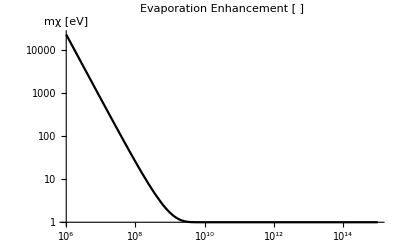

```mathematica
EvapRescale/.vesc->"vesc"/.βE->"βcore"/.EarthRepl/.mχ->mχ("JpereV")/("c")^2/.SIConstRepl//Simplify//PowerExpand
LogLogPlot[%,{mχ,10^6,10^15},PlotLabel->"Evaporation Enhancement [ ]",AxesLabel->"mχ [eV]",PlotStyle->Black]
```

```mathematica
EvapRescale/.vesc->x/(√(mχ βE))//PowerExpand
Limit[%^-1,x->0]
```

1/(-ⅇ^(-x^2/2) √(2/π) x+Erf[x/(√2)])

0

### Analytic Expression for flux / speed dist at Earth

#### Analytic speed dist at Earth - from appendix

Flux density at ∞ is

- n_p_D f_∞(v_∞)  ∫_(toward Earth) dΩ  v.r̂ 

Angular Integral of v . r̂ = v∞ cosθ is

```mathematica
2 π Integrate[Subscript[v, ∞] cosθ^2,{cosθ,0,1}]
```

(2 π v_∞)/3

So just do (2π)/3 times the gravitationally focussed boltzmann distribution, times a factor of number density

ϕ_∞ = - n_p_D f_∞(v_∞)  v_∞ (2π)/3 

This is INCOMING flux density, total flux is zero

So the incoming rate is then

ϕ_∞ A_∞ = - n_p_D f_∞(v_∞)  v_∞ (2π)/3 4 π (r_∞)^2

** ** caveat is we need to constrain the integral so that only the particles with impact parameter low enough to reach a given r are included. This expression diverges in the limit r_∞ -> ∞

```mathematica
cosθ = vr/v
```

```mathematica
"The f in this expression is normalized to ∫dv f=n. Which is MB times a factor of n."
Integrate[(vr∞)/(√((vr∞)^2 + vesc^2)) 1/(v∞),vr∞]
(%/.vr∞->-v∞) - (%/.vr∞->-√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)))//FullSimplify//PowerExpand//Simplify
unnormedvdistatearth=2 (r∞)^2/r^2 f[r∞,v∞]D[√(v^2-vesc^2),v]Normal@Series[%,{r∞,∞,2}]/.vesc->√(v^2-(v∞)^2)//PowerExpand
Print["Factor of 2 from other velocity sign. \n \n Note that they normalize as ∫dv f = n but don't inclue the jacobian for velocity volume (v^2) in f. So f is just e^(-β FractionBox[m, 2] SuperscriptBox[v, 2]). This means that this final expression, with the factor of w is simply. f = v^2 e^(-β FractionBox[m, 2] (SuperscriptBox[v, 2] - SubscriptBox[SuperscriptBox[v, 2], esc]))"]
```

The f in this expression is normalized to ∫dv f=n. Which is MB times a factor of n.

(√(vesc^2+(vr∞)^2))/(v∞)

((r∞-√(-r^2+(r∞)^2)) √(vesc^2+(v∞)^2))/(r∞ v∞)

(v^2 f[r∞,v∞])/(v∞)^2

Factor of 2 from other velocity sign. 
 
 Note that they normalize as ∫dv f = n but don't inclue the jacobian for velocity volume (v^2) in f. So f is just e^(-β FractionBox[m, 2] SuperscriptBox[v, 2]). This means that this final expression, with the factor of w is simply. f = v^2 e^(-β FractionBox[m, 2] (SuperscriptBox[v, 2] - SubscriptBox[SuperscriptBox[v, 2], esc]))

```mathematica
Integrate[v^2 E^(-β m/2 v^2),{v,0,∞}]//Normal
Normofveldist=A/.Solve[n ==A %,A][[1]]
```

(√(π/2))/(m β)^(3/2)

n √(2/π) (m β)^(3/2)

```mathematica
vdistatearth=Normofveldist unnormedvdistatearth/.f->(#2^2 E^(-β m/2#2^2)&)/.v∞->√(v^2-vesc^2)
```

ⅇ^(-1/2 m (v^2-vesc^2) β) n √(2/π) v^2 (m β)^(3/2)

```mathematica
natEarth =Integrate[vdistatearth,{v,0,∞}]
```

ConditionalExpression[ⅇ^(1/2 m vesc^2 β) n, Re[m β]>0]

```mathematica
vrintermsofbE=vr/.Solve[bE==rE vperp/vr/.vperp->√(v^2-vr^2),vr][[2]]//Simplify//PowerExpand
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(rE v)/(√(bE^2+rE^2))

#### Flux at Earth - from appendix

```mathematica
ϕE = vdistatearth vrintermsofbE
```

(ⅇ^(-1/2 m (v^2-vesc^2) β) n √(2/π) rE v^3 (m β)^(3/2))/(√(bE^2+rE^2))

```mathematica
Integrate[(vr∞)^2/(√((vr∞)^2 + vesc^2)) 1/(v∞),vr∞]
(%/.vr∞->v∞) - (%/.vr∞->√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)))//FullSimplify//PowerExpand//Simplify
unnormedvfluxdistEarth= (r∞)^2/r^2 f[r∞,v∞]D[√(v^2-vesc^2),v]Normal@Series[%,{r∞,∞,2}]/.vesc->√(v^2-(v∞)^2)//PowerExpand//Simplify
Print["No factor of 2 here since we only want the incoming flux."]
```

(1/2 vr∞ √(vesc^2+(vr∞)^2)+1/2 vesc^2 Log[-vr∞+√(vesc^2+(vr∞)^2)])/(v∞)

1/(2 r∞ v∞)(√(vesc^2+(v∞)^2) (r∞ v∞-√(-r^2+(r∞)^2) √((v∞)^2-(r^2 (vesc^2+(v∞)^2))/(r∞)^2))+r∞ vesc^2 Log[-v∞+√(vesc^2+(v∞)^2)]-r∞ vesc^2 Log[(√(-r^2+(r∞)^2) √(vesc^2+(v∞)^2))/(r∞)-√((v∞)^2-(r^2 (vesc^2+(v∞)^2))/(r∞)^2)])

(v^2 f[r∞,v∞])/(2 v∞)

No factor of 2 here since we only want the incoming flux.

```mathematica
Print["Maybe this is right?"]
Integrate[vr∞  1/(v∞),vr∞]
(%/.vr∞->v∞) - (%/.vr∞->√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)))//FullSimplify//PowerExpand//Simplify
unnormedvfluxdistEarth= (r∞)^2/r^2 f[r∞,v∞]D[√(v^2-vesc^2),v]Normal@Series[%,{r∞,∞,2}]/.vesc->√(v^2-(v∞)^2)//PowerExpand//Simplify
Print["No factor of 2 here since we only want the incoming flux."]
```

Maybe this is right?

(vr∞)^2/(2 v∞)

(r^2 (vesc^2+(v∞)^2))/(2 (r∞)^2 v∞)

(v^3 f[r∞,v∞])/(2 (v∞)^2)

No factor of 2 here since we only want the incoming flux.

```mathematica
vfluxdistatearth=Normofveldist unnormedvfluxdistEarth/.f->(#2^2 E^(-β m/2#2^2)&)/.v∞->√(v^2-vesc^2)
```

(ⅇ^(-1/2 m (v^2-vesc^2) β) n v^2 √(v^2-vesc^2) (m β)^(3/2))/(√(2 π))

```mathematica
fluxatEarth=Integrate[vfluxdistatearth,{v,vesc,∞}]//PowerExpand
```

ConditionalExpression[(ⅇ^(1/4 m vesc^2 β) √m n vesc^2 √β BesselK[1,1/4 m vesc^2 β])/(2 √(2 π)), Re[vesc]>0&&Im[vesc]==0&&Re[m β]>0]

```mathematica
Normal@fluxatEarth
```

(ⅇ^(1/4 m vesc^2 β) √m n vesc^2 √β BesselK[1,1/4 m vesc^2 β])/(2 √(2 π))

Units here are v n ([mβ] =[1/v^2])

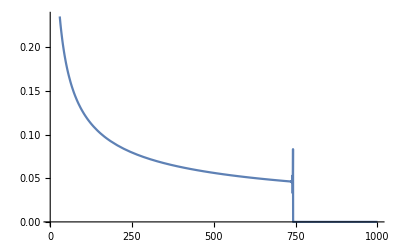

```mathematica
Plot[BesselK[1,x] E^x,{x,1,1000}]
```

(ⅇ^-x √(π/2))/(√x)

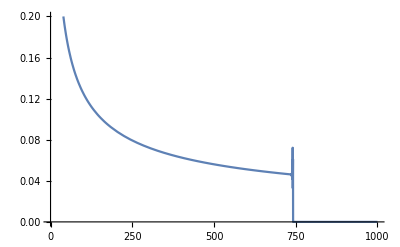

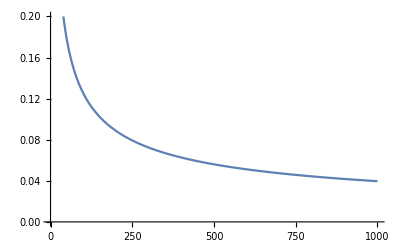

```mathematica
Normal@Series[BesselK[1,x],{x,∞,1}]
Plot[%E^x,{x,1,1000},PlotRange->{0,0.2}]
Plot[√(π/(2 x)),{x,1,1000},PlotRange->{0,0.2}]
```

```mathematica
Series[BesselK[1,x],{x,∞,1}]
```

ⅇ^(-x+O[1/x]^2) (√(π/2) √(1/x)+O[1/x]^(3/2))

So at low temperatures compared to mχ vesc^2 the flux goes as 1/(√ratio)

## Dielectric Analytics

### Electron Contribution to Evaporation Rate - momentum expansion

#### Analysis used in notes

Electronic evaporation is suppressed by the degeneracy of the fermi gas. But we want to find an estimate to show that it can be neglected. 

The contribution will only have support near the fermi momentum. We can then expand near the fermi momentum

```mathematica
"D"/.FeTotalparams
"D"/.SiO2Totalparams
"D"/.MgOTotalparams
```

{322.436,485.073,837.295,3156.08,81222.,1.70758×10^6}

{801.791,2326.72}

{412.839,736.197,841.135,2012.33}

How do we compute energy lost? Intuitively it is from a negative k. But does this make sense? Or is it negative k and negative ω? 

Is it sensible to compute the difference between the pure degenerate and slightly degenerate cases? The dielectric is odd in k and ω. So we should be able to integrate over the forbidden region, then using the fact that ϵ(-k,-ω) = ϵ(k,ω) we can compute as we did before and interpret as the rate for E_(p+k)<E_k (amounts to reinterpretting ω and using evenness in k)

Just use series in small ζ-1, and find the integration region that way.

```mathematica
FOccn = 1/(E^(β(Ek - μ))+1)
Series[FOccn,{Ek,μ,1}]
Assuming[Ek-μ>0,Series[FOccn,{β,∞,1}]]
```

1/(1+ⅇ^(β (Ek-μ)))

1/2-1/4 β (Ek-μ)+O[Ek-μ]^2

1/(1+ⅇ^((Ek-μ) β+O[1/β]^2))

```mathematica
FOccnDζ = 1/(1+ⅇ^(D (-1+ζ^2)))
```

1/(1+ⅇ^(D (-1+ζ^2)))

300

16

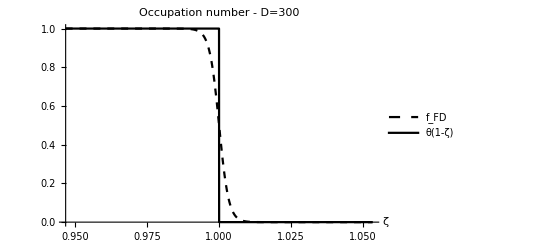

```mathematica
Dtemp = 300
rangerescale=8 * 2
Show[{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-rangerescale/Dtemp,1 + rangerescale/Dtemp},PlotRange->All,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{Directive[Black,Dashed],Black},{"f_FD","θ(1-ζ)"}],PlotLabel->"Occupation number - D=300",AxesLabel->Automatic],
Plot[(HeavisideTheta[1-ζ]),{ζ,1-rangerescale/Dtemp,1 + rangerescale/Dtemp},PlotStyle->Black,PlotRange->All,AxesLabel->Automatic,Exclusions->None]}]
```

```mathematica
FOccnDζnearkF=Series[FOccnDζ,{ζ,1,1}]//Normal//FullSimplify
```

1/2 (1+D-D ζ)

```mathematica
FOccn /. μ-> EF + π^2/12 1/(D β)
%/.β->D/EF/.Ek->EF ζ^2//Simplify
Series[%,{ζ,1,1}]//Normal//FullSimplify
FOccnDζwμcor=Series[%,{D,∞,1}]//Normal //Simplify
"So we can neglect the change in the chemical potential here. "
```

1/(1+ⅇ^((-EF+Ek-π^2/(12 D β)) β))

1/(1+ⅇ^(-π^2/(12 D)+D (-1+ζ^2)))

(ⅇ^(π^2/(12 D)) (1+ⅇ^(π^2/(12 D))-2 D (-1+ζ)))/((1+ⅇ^(π^2/(12 D)))^2)

1/2+(π^2 (24+π^2 (-1+ζ)))/(1152 D)-1/2 D (-1+ζ)

So we can neglect the change in the chemical potential here.

```mathematica
ϵnd[u,z,uν]
```

1+1/(4 z^3)χ^2 (1/D-z) (ⅈ (ArcTan[(1+u-z)/uν]+ArcTan[(1-u+z)/uν])-ⅈ (ArcTan[(1-u-z)/uν]+ArcTan[(1+u+z)/uν])-1/2 Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/2 Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)])

```mathematica
ζm/."D"->100
```

99/100

```mathematica
Solve[FOccnDζnearkF==1,ζ]//Simplify
Solve[FOccnDζnearkF==0,ζ]//Simplify
```

{{ζ→(-1+D)/D}}

{{ζ→1+1/D}}

300

16

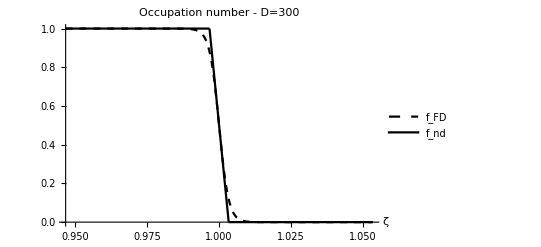

```mathematica
Dtemp = 300
rangerescale=8 * 2
Show[{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-rangerescale/Dtemp,1 + rangerescale/Dtemp},PlotRange->All,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{Directive[Black,Dashed],Black},{"f_FD","f_nd"}],PlotLabel->"Occupation number - D=300",AxesLabel->Automatic],Plot[(FOccnDζnearkF/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-ζ],{ζ,1-rangerescale/Dtemp,1-1/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-ζ],{ζ,1+1/Dtemp,1+rangerescale/Dtemp},PlotRange->All,PlotStyle->Black]}]
```

#### Compute complex ω RPA dielectric in large D limit

```mathematica
Series[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],{D,∞,2}]//Normal
Expandedfndintegrand = ((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D);
# Log[((a+#)^2+uν^2)/((a-#)^2+uν^2)]&;
Series[Expandedfndintegrand/.f->%,{D,∞,1}]//Normal//FullSimplify;
δχRe1=Integrate[%,{ζ,0,1}]//FullSimplify

-# (ArcTan[(a+#)/uν]-ArcTan[(a-#)/uν])&;
Series[Expandedfndintegrand/.f->%,{D,∞,1}]//Normal//FullSimplify;
δχIm1=Integrate[%,{ζ,0,1}]//FullSimplify
```

∫_0^1 (((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D))ⅆζ

Log[1+(4 a)/((-1+a)^2+uν^2)]/D

(ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν])/D

```mathematica
"Now compute the dielectric"
δϵRe1 = 1+χ^2/z^2 1/(4 z)(((δχRe1+I δχIm1)/.a->u+z)-((δχRe1+I δχIm1)/.a->u-z))//Simplify
```

Now compute the dielectric

1-1/(4 D z^3)ⅈ χ^2 (ArcTan[(-1+u-z)/uν]-ArcTan[(1+u-z)/uν]-ArcTan[(-1+u+z)/uν]+ArcTan[(1+u+z)/uν]-ⅈ Log[1+(4 (u-z))/(uν^2+(1-u+z)^2)]+ⅈ Log[1+(4 (u+z))/(uν^2+(-1+u+z)^2)])

```mathematica
Series[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],{D,∞,2}]//Normal
Expandedfndintegrand = ((1+ζ) f[1-ζ/D])/(2 D);
#/2 Log[((a+#)^2+uν^2)/((a-#)^2+uν^2)]&;
Series[Expandedfndintegrand/.f->%,{D,∞,2}]//Normal//FullSimplify;
δχRe2=Integrate[%,{ζ,-1,1}]//FullSimplify

-# (ArcTan[(a+#)/uν]-ArcTan[(a-#)/uν])&;
Series[Expandedfndintegrand/.f->%,{D,∞,2}]//Normal;
δχIm2=Integrate[%,{ζ,-1,1}]
```

∫_0^1 (((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D))ⅆζ

(-(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2)+(-1+3 D) Log[1+(4 a)/((-1+a)^2+uν^2)])/(6 D^2)

1/(6 D^2)((4 uν (1+a^2+uν^2))/((-1+a^2)^2+2 (1+a^2) uν^2+uν^4)+(-2+6 D) ArcTan[(-1+a)/uν]+(2-6 D) ArcTan[(1+a)/uν])

```mathematica
"Now compute the dielectric"
δϵRe2 = 1+χ^2/z^2 1/(4 z)(((δχRe2+I δχIm2)/.a->u+z)-((δχRe2+I δχIm2)/.a->u-z))//FullSimplify
```

Now compute the dielectric

1+1/(24 D^2 z^3)χ^2 (2 (1/(-1+u+ⅈ uν-z)+1/(1+u+ⅈ uν-z)-1/(-1+u+ⅈ uν+z)-1/(1+u+ⅈ uν+z))+2 ⅈ (-1+3 D) ArcTan[(1+u-z)/uν]+2 ⅈ (-1+3 D) ArcTan[(1-u+z)/uν]+(-1+3 D) (2 ⅈ ArcTan[(-1+u+z)/uν]-2 ⅈ ArcTan[(1+u+z)/uν]-Log[1+(4 (u-z))/(uν^2+(1-u+z)^2)]+Log[1+(4 (u+z))/(uν^2+(-1+u+z)^2)]))

#### Decomposition of 2nd order corrections

```mathematica
(4 uν (1+a^2+uν^2))/((-1+a^2)^2+2 (1+a^2) uν^2+uν^4)//Apart
2 uν(1/(1+(a-uν)^2)+1/(1+(a+uν)^2))//Apart
 uν(1/(1+I(a-uν))+1/(1-I(a-uν))+1/(1+I(a+uν))+1/(1-I(a+uν)))//Simplify//Apart
```

(2 uν)/(1-2 a+a^2+uν^2)+(2 uν)/(1+2 a+a^2+uν^2)

(2 uν)/(1+a^2-2 a uν+uν^2)+(2 uν)/(1+a^2+2 a uν+uν^2)

(2 uν)/(1+a^2-2 a uν+uν^2)+(2 uν)/(1+a^2+2 a uν+uν^2)

```mathematica
(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2)//Apart
2((a-1)/(1+(a-uν)^2)+(1+a)/(1+(a+uν)^2))//Apart
```

(2 (-1+a))/(1-2 a+a^2+uν^2)+(2 (1+a))/(1+2 a+a^2+uν^2)

(2 (-1+a))/(1+a^2-2 a uν+uν^2)+(2 (1+a))/(1+a^2+2 a uν+uν^2)

```mathematica
(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2)/.uν->0//Apart
```

2/(-1+a)+2/(1+a)

#### Limits of 2nd order corrections in large and small a

Check that the expansion works for large and small a

```mathematica
Series[ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν],{a,0,2}]
Series[ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν],{a,∞,2}]
Series[(4 uν (1+a^2+uν^2))/((-1+a^2)^2+2 (1+a^2) uν^2+uν^4),{a,0,2}]
Series[(4 uν (1+a^2+uν^2))/((-1+a^2)^2+2 (1+a^2) uν^2+uν^4),{a,∞,2}]
"Both terms in the expansion scale the same way with large and small a so we don't have to worry about subleading terms becoming dominant."
```

-2 ArcTan[1/uν]+(2 uν a^2)/((1+uν^2)^2)+O[a]^3

-(2 uν)/a^2+O[1/a]^3

(4 uν)/(1+uν^2)-(4 (uν (-3+uν^2)) a^2)/((1+uν^2)^3)+O[a]^3

(4 uν)/a^2+O[1/a]^3

Both terms in the expansion scale the same way with large and small a so we don't have to worry about subleading terms becoming dominant.

```mathematica
Series[Log[1+(4 a)/((-1+a)^2+uν^2)],{a,0,2}]
Series[Log[1+(4 a)/((-1+a)^2+uν^2)],{a,∞,2}]
Series[(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2),{a,0,2}]
Series[(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2),{a,∞,2}]
"Both terms in the expansion scale the same way with large and small a so we don't have to worry about subleading terms becoming dominant."
```

(4 a)/(1+uν^2)+O[a]^3

4/a+O[1/a]^3

(4 (-1+uν^2) a)/((1+uν^2)^2)+O[a]^3

4/a+O[1/a]^3

Both terms in the expansion scale the same way with large and small a so we don't have to worry about subleading terms becoming dominant.

#### Real RPA limits of above

```mathematica
"The 1st order corrections are straightforward using expressions in the notes."
(Log[(1+a)/(1-a)]/.a->z)-(Log[(1+a)/(1-a)]/.a->-z)
%==2Log[(1+z)/(1-z)]//Simplify//PowerExpand
```

The 1st order corrections are straightforward using expressions in the notes.

-Log[(1-z)/(1+z)]+Log[(1+z)/(1-z)]

True

#### Scattering Phase space

The maximum momentum transfer in ζ we can have in an interaction is

```mathematica
Δζmax = (1+1/D)-(1-1/D)
```

2/D

We have defined fermi function to only have support over this range, since we have defined p = ζ k_F we have that the maximum momentum that can be transfered to the probe from the system for each oscillator is in eV

```mathematica
2/("D")"qF"("ℏ""c")/("JpereV")/.FeTotalparams
2/("D")"qF"("ℏ""c")/("JpereV")/.SiO2Totalparams
2/("D")"qF"("ℏ""c")/("JpereV")/.MgOTotalparams
```

{17.8171,14.5263,11.0565,5.69488,1.12259,0.244832}

{11.2987,6.63264}

{15.7459,11.7913,11.0313,7.13196}

So there is some possibility to evaporate light mass aDM with these kinematics. However, all rates will be suppressed by

```mathematica
"D"/.FeTotalparams
"D"/.SiO2Totalparams
"D"/.MgOTotalparams
```

{322.436,485.073,837.295,3156.08,81222.,1.70758×10^6}

{801.791,2326.72}

{412.839,736.197,841.135,2012.33}

```mathematica
1/("D")/.FeTotalparams
1/("D")/.SiO2Totalparams
1/("D")/.MgOTotalparams
```

{0.00310139,0.00206155,0.00119432,0.000316849,0.0000123119,5.85624×10^-7}

{0.00124721,0.000429789}

{0.00242225,0.00135833,0.00118887,0.000496936}

```mathematica
"Need to recompute the dielectric imposing this kinematic restriction"
Series[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],{D,∞,2}]//Normal
Expandedfndintegrand = ((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D);
# Log[((a+#)^2+uν^2)/((a-#)^2+uν^2)]&;
Series[Expandedfndintegrand/.f->%,{D,∞,1}]//Normal//FullSimplify;
δχRe1=Integrate[%,{ζ,0,1}]//FullSimplify

-# (ArcTan[(a+#)/uν]-ArcTan[(a-#)/uν])&;
Series[Expandedfndintegrand/.f->%,{D,∞,1}]//Normal//FullSimplify;
δχIm1=Integrate[%,{ζ,0,1}]//FullSimplify
```

Need to recompute the dielectric imposing this kinematic restriction

∫_0^1 (((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D))ⅆζ

Log[1+(4 a)/((-1+a)^2+uν^2)]/D

(ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν])/D

```mathematica
Series[Integrate[FOccnDζnearkF f[ζ],{ζ,0,1+1/D}],{D,∞,2}]//Normal
```

∫_0^(1+1/D) 1/2 (1+D-D ζ) f[ζ]ⅆζ

```mathematica
Limit[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],D->∞]
"Since f is assumed regular at ζ=1 we have in the limit that D->∞ the integrand"
f[1]Integrate[D (1-ζ) ,{ζ,1-1/D,1+1/D}]
(*(%/.ζ->1-1/D)//Simplify
(%%/.ζ->1+1/D)//Simplify*)
"Which means that in the expansion of the integral in large D, the 0th order term vanishes. So the next term is"
HoldForm[1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],D]]
1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],D]//Simplify
```

lim_(D→∞) ∫_(1-1/D)^(1+1/D) 1/2 (1+D-D ζ) f[ζ]ⅆζ

Since f is assumed regular at ζ=1 we have in the limit that D->∞ the integrand

0

Which means that in the expansion of the integral in large D, the 0th order term vanishes. So the next term is

(∂_D ∫_(1-1/D)^(1+1/D) FOccnDζnearkF f[ζ]ⅆζ)/D

(-f[(-1+D)/D]+D^2 ∫_((-1+D)/D)^(1+1/D) -1/2 (-1+ζ) f[ζ]ⅆζ)/D^3

```mathematica
Limit[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D-2z}],D->∞]
"Since f is assumed regular at ζ=1 we have in the limit that D->∞ the integrand"
f[1]Integrate[D (1-ζ) ,{ζ,1-1/D,1+1/D-2z}]
(*(%/.ζ->1-1/D)//Simplify
(%%/.ζ->1+1/D)//Simplify*)
"Which means that in the expansion of the integral in large D, the 0th order term vanishes. So the next term is"
HoldForm[1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D-2z}],D]]
"We can now seperate the integrals"
1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,0,1+1/D-2z}],D]//Simplify
-1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,0,1-1/D}],D]//Simplify
"Then perform shifts on the variable so that"
1/D D[Integrate[FOccnDζnearkF f[ζ]/.ζ->ζ-(1/D-2z),{ζ,-1/D+2z,1}],D]//Simplify
-1/D D[Integrate[FOccnDζnearkF f[ζ]/.ζ->ζ+1/D,{ζ,-1/D,1}],D]//Simplify
```

lim_(D→∞) ∫_(1-1/D)^(1+1/D-2 z) 1/2 (1+D-D ζ) f[ζ]ⅆζ

Since f is assumed regular at ζ=1 we have in the limit that D->∞ the integrand

(2 z-2 D z^2) f[1]

Which means that in the expansion of the integral in large D, the 0th order term vanishes. So the next term is

(∂_D ∫_(1-1/D)^(1+1/D-2 z) FOccnDζnearkF f[ζ]ⅆζ)/D

We can now seperate the integrals

(-z f[1+1/D-2 z]+D ∫_0^(1+1/D-2 z) -1/2 (-1+ζ) f[ζ]ⅆζ)/D^2

-(f[(-1+D)/D]+D^2 ∫_0^((-1+D)/D) -1/2 (-1+ζ) f[ζ]ⅆζ)/D^3

Then perform shifts on the variable so that

((-3+D (-1+4 z)) f[-2/D+4 z])/(2 D^3)+1/D(∫_(-1/D+2 z)^1 1/2 (-((-1+2 z+ζ) f[-1/D+2 z+ζ])+((2-D (-1+2 z+ζ)) f'[-1/D+2 z+ζ])/D^2)ⅆζ)

(f[0]+D f[0]-2 D^2 ∫_(-1/D)^1 -((-1+ζ) (D f[1/D+ζ]-f'[1/D+ζ]))/(2 D)ⅆζ)/(2 D^3)

#### Investigate changing slope to conservatively overestimate phase space available

Consider conservatively rescaling the slope of the line to ensure that the phase space that the line doesn’t capture is fermi suppressed.

```mathematica
1/(1+ⅇ^(D (-1+ζ^2)))/.ζ->1+b/D//Simplify
%/.b->5/.D->10000000//Simplify//N
(*1/(1+E^(2 b))*)E^(-2 b)/.b->5//N
1/(1+ⅇ^(D (-1+ζ^2)))/.ζ->1-b/D//Simplify
1-%/.b->5/.D->10000000//Simplify//N
"So we see that in the limit of large D a rescaling of D -> D/b gives a fermi suppression at the boundaries of about E^(-2 b)"
"So our fermi suppression is about 10^-b"
(Log10@(E^(-2 b)))//Simplify//PowerExpand
N@(Log[10])
```

1/(1+ⅇ^((b (b+2 D))/D))

0.0000453978

0.0000453999

1/(1+ⅇ^((b (b-2 D))/D))

0.000045398

So we see that in the limit of large D a rescaling of D -> D/b gives a fermi suppression at the boundaries of about E^(-2 b)

So our fermi suppression is about 10^-b

-(2 b)/(Log[2]+Log[5])

2.30259

```mathematica
E^-16//N
```

1.12535×10^-7

300

8

2

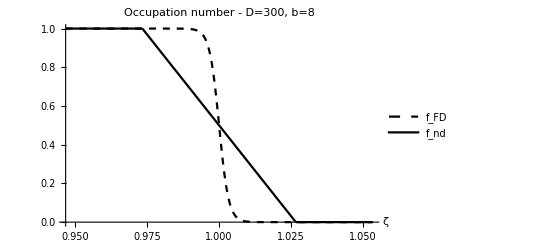

```mathematica
Clear[rangerescale]
Dtemp = 300
sloperescale=8
rangerescale = 2

Show[{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-(rangerescale sloperescale)/Dtemp,1 + (rangerescale sloperescale)/Dtemp},PlotRange->All,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{Directive[Black,Dashed],Black},{"f_FD","f_nd"}],PlotLabel->"Occupation number - D=300, b=8",AxesLabel->Automatic],Plot[(FOccnDζnearkF/.D->D/sloperescale/.D->Dtemp),{ζ,1-sloperescale/Dtemp,1 + sloperescale/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-ζ],{ζ,1-(rangerescale sloperescale)/Dtemp,1-sloperescale/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-ζ],{ζ,1+sloperescale/Dtemp,1+(rangerescale sloperescale)/Dtemp},PlotRange->All,PlotStyle->Black]}]
```

#### Expand in small and large exponentials

1-x+O[x]^2

1/x+O[1/x]^2

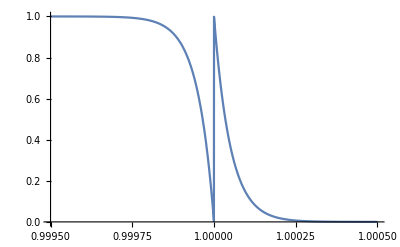

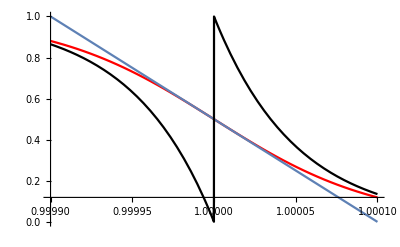

```mathematica
Series[1/(1+x),{x,0,1}]
Series[1/(1+x),{x,∞,1}]
Dtemp = 10000;
Plot[HeavisideTheta[1-ζ](1- x)+HeavisideTheta[ζ-1](x^-1)/.x->ⅇ^(D (-1+ζ^2))/.D->Dtemp,{ζ,1-5/Dtemp,1 + 5/Dtemp}]
Show@{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All,PlotStyle->Red],Plot[(FOccnDζnearkF/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All],Plot[HeavisideTheta[1-ζ](1- x)+HeavisideTheta[ζ-1](x^-1)/.x->ⅇ^(D (-1+ζ^2))/.D->Dtemp,{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotStyle->Black]}
```

1-x+x^2+O[x]^3

1/x-(1/x)^2+O[1/x]^3

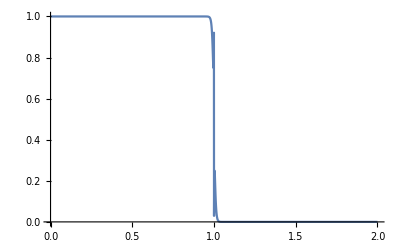

10000

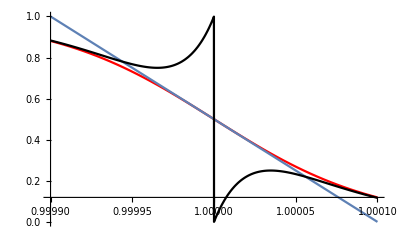

```mathematica
Series[1/(1+x),{x,0,2}]
Series[1/(1+x),{x,∞,2}]
Plot[HeavisideTheta[1-ζ](1- x+x^2)+HeavisideTheta[ζ-1](x^-1-x^-2)/.x->ⅇ^(D (-1+ζ^2))/.D->100,{ζ,0,2}]
Dtemp = 10000
Show@{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All,PlotStyle->Red],Plot[(FOccnDζnearkF/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All],Plot[HeavisideTheta[1-ζ](1- x+x^2)+HeavisideTheta[ζ-1](x^-1-x^-2)/.x->ⅇ^(D (-1+ζ^2))/.D->Dtemp,{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotStyle->Black]}
```

So our linear approximation is a better fit than expanding in large and small exponentials near the fermi sphere. 

It does givea much better approximation far from the fermi sphere. The question is whether we think the most important contribution to the evaporation rate will be far or close to the fermi sphere. I suppose we can check this by computing the contribution from this expansion. 

The other intriguing part of using this expansion, is that each subsequent term amounts to a change of the value of the degeneracy by an integer, so in principle they could be resummed. So we only need to compute:

```mathematica
Series[1/(1+x),{x,0,2}](*valid between 0 and 1*)
Series[1/(1+x),{x,∞,2}](*valid between 1 and ∞*)
```

1-x+x^2+O[x]^3

1/x-(1/x)^2+O[1/x]^3

```mathematica
Integrate[1/2 ζ E^(D(ζ^2-1))Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)],{ζ,0,1}]
```

$Aborted

Try integrating by parts for imaginary part

```mathematica
1/2 ζ E^(D(ζ^2-1))Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)](*this is boundary term at 0 and ∞*)
Integrate[1/2 ζ E^(D(ζ^2-1)),ζ]
D[Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)],ζ]//FullSimplify(*this is boundary term at 0 and ∞*)
Apart[%,ζ]
Integrate[%% %%%,ζ]
```

1/2 ⅇ^(D (-1+ζ^2)) ζ Log[(uν^2+(a+ζ)^2)/(uν^2+(a-ζ)^2)]

(ⅇ^(-D+D ζ^2))/(4 D)

(4 a (a^2+uν^2-ζ^2))/(a^4+2 a^2 (uν-ζ) (uν+ζ)+(uν^2+ζ^2)^2)

(2 (a-ζ))/(a^2+uν^2-2 a ζ+ζ^2)+(2 (a+ζ))/(a^2+uν^2+2 a ζ+ζ^2)

(a ∫(ⅇ^(-D+D ζ^2) (a^2+uν^2-ζ^2))/(a^4+2 a^2 (uν-ζ) (uν+ζ)+(uν^2+ζ^2)^2)ⅆζ)/D

Try integrating by parts for the real part

```mathematica
- ζ  E^(D(ζ^2-1))(ArcTan[(a+ζ)/uν]-ArcTan[(a-ζ)/uν])
 Integrate[ζ E^(D(ζ^2-1)),ζ]
D[(ArcTan[(a+ζ)/uν]-ArcTan[(a-ζ)/uν]),ζ]
Apart[%,ζ]
Integrate[%% %%%,ζ]
```

-ⅇ^(D (-1+ζ^2)) ζ (-ArcTan[(a-ζ)/uν]+ArcTan[(a+ζ)/uν])

(ⅇ^(-D+D ζ^2))/(2 D)

1/(uν (1+(a-ζ)^2/uν^2))+1/(uν (1+(a+ζ)^2/uν^2))

uν/(a^2+uν^2-2 a ζ+ζ^2)+uν/(a^2+uν^2+2 a ζ+ζ^2)

(∫ⅇ^(-D+D ζ^2) (1/(uν (1+(a-ζ)^2/uν^2))+1/(uν (1+(a+ζ)^2/uν^2)))ⅆζ)/(2 D)

We can differentiate under the integral sign to solve both these integrals.

```mathematica
Integrate[E^(D (ζ^2-1)),{ζ,0,1}]
```

(ⅇ^-D √π Erfi[√D])/(2 √D)

```mathematica
DSolve[(a^2+uν^2)f[D]+2 a f'[D]+f''[D]==uν(ⅇ^-D √π Erfi[√D])/(2 √D),f[D],D]//Simplify
```

{{f[D]→-(ⅈ ⅇ^(-a D+ⅈ D uν) π)/(4 √(-1+a-ⅈ uν))+(ⅈ ⅇ^(-D (a+ⅈ uν)) π)/(4 √(-1+a+ⅈ uν))+ⅇ^(-D (a+ⅈ uν)) C[1]+ⅇ^(-a D+ⅈ D uν) C[2]-(ⅈ ⅇ^(-a D+ⅈ D uν) π OwenT[ⅈ √2 √D √(-1+a-ⅈ uν),1/(√(-1+a-ⅈ uν))])/(√(-1+a-ⅈ uν))+(ⅈ ⅇ^(-D (a+ⅈ uν)) π OwenT[ⅈ √2 √D √(-1+a+ⅈ uν),1/(√(-1+a+ⅈ uν))])/(√(-1+a+ⅈ uν))}}

```mathematica
Integrate[E^(-D (ζ^2-1)),{ζ,1,∞}]
```

ConditionalExpression[(ⅇ^D √π Erfc[√D])/(2 √D), Re[D]>0]

```mathematica
DSolve[(a^2+uν^2)f[D]+2 a f'[D]+f''[D]==uν(ⅇ^-D √π Erfc[√D])/(2 √D),f[D],D]//FullSimplify
```

{{f[D]→1/4 ⅇ^(-D (a+ⅈ uν)) (-ⅈ π ((ⅇ^(2 ⅈ D uν) √(-1+a-ⅈ uν))/(√((ⅈ (-1+a)+uν)^2))+(√((ⅈ-ⅈ a+uν)^2))/(-1+a+ⅈ uν)^(3/2))+4 (C[1]+ⅇ^(2 ⅈ D uν) C[2])-ⅈ π ((ⅇ^(2 ⅈ D uν) √(1-a+ⅈ uν) Erfi[√D √(-1+a-ⅈ uν)])/(√((ⅈ (-1+a)+uν)^2))+(√((ⅈ-ⅈ a+uν)^2) Erfi[√D √(-1+a+ⅈ uν)])/(1-a-ⅈ uν)^(3/2))-4 ⅈ π ((√(-(-1+a+ⅈ uν)^2) OwenT[√2 √D √(1-a-ⅈ uν),1/(√(1-a-ⅈ uν))])/(-1+a+ⅈ uν)^(3/2)+(ⅇ^(2 ⅈ D uν) √(-1+a-ⅈ uν) OwenT[√2 √D √(1-a+ⅈ uν),1/(√(1-a+ⅈ uν))])/(√((ⅈ (-1+a)+uν)^2))))}}

No way that we can sum this over D times an integer. But we can use this to get the non-degenerate limit

```mathematica
Integrate[E^(D (ζ^2-1)),{ζ,0,∞}]//Normal
DSolve[(a^2+uν^2)f[D]+2 a f'[D]+f''[D]==uν%,f[D],D]//FullSimplify
```

(ⅇ^-D √π)/(2 √-D)

{{f[D]→1/(4 √-D)ⅇ^(-D (a+ⅈ uν)) (4 √-D (C[1]+ⅇ^(2 ⅈ D uν) C[2])-ⅈ D √π (ExpIntegralE[1/2,-D (-1+a+ⅈ uν)]-ⅇ^(2 ⅈ D uν) ExpIntegralE[1/2,D-a D+ⅈ D uν]))}}

```mathematica
1/(4 √-D)ⅇ^(-D (a+ⅈ uν)) (4 √-D (C[1]+ⅇ^(2 ⅈ D uν) C[2])-ⅈ D √π (ExpIntegralE[1/2,-D (-1+a+ⅈ uν)]-ⅇ^(2 ⅈ D uν) ExpIntegralE[1/2,D-a D+ⅈ D uν]))/.C[1]->0/.C[2]->0/.{a->2,uν->3,D->-100}//N
```

7.13967×10^41+7.25355×10^24 ⅈ

```mathematica
Integrate[E^(D (ζ^2))ζ,{ζ,0,∞}]
```

ConditionalExpression[-1/(2 D), Re[D]<0]

```mathematica
(ζ^2 E^(D (ζ^2-1)))/(u+z+ζ y + I uν)
Integrate[ζ^2 E^(-D (ζ^2-1)),{ζ,0,∞}]
```

(ⅇ^(D (-1+ζ^2)) ζ^2)/(u+ⅈ uν+z+y ζ)

ConditionalExpression[(ⅇ^D √π)/(4 D^(3/2)), Re[D]>0]

```mathematica
DSolve[(u+ⅈ uν+z) f[D]-y  f'[D]==(ⅇ^D √π)/(4 D^(3/2)),f[D],D]//FullSimplify
```

{{f[D]→1/2 ((ⅇ^D √π)/(√D y)+2 ⅇ^((D (u+ⅈ uν+z))/y) C[1]+(ⅇ^((D (u+ⅈ uν+z))/y) π √(u+ⅈ uν-y+z) Erf[(√D √(u+ⅈ uν-y+z))/(√y)])/y^(3/2))}}

```mathematica
Integrate[1/2 ((ⅇ^D √π)/(√D y)+2 ⅇ^((D (u+ⅈ uν+z))/y) C[1]+(ⅇ^((D (u+ⅈ uν+z))/y) π √(u+ⅈ uν-y+z) Erf[(√D √(u+ⅈ uν-y+z))/(√y)])/y^(3/2)),{y,-1,1}]
```

$Aborted

#### Use the form in notes for large and small exponentials

```mathematica
Integrate[(E^(- D ζ^2))/(a - ζ + i uν),{ζ,0,∞}]
```

ConditionalExpression[1/2 ⅇ^(-D (a+i uν)^2) (CoshIntegral[D (a+i uν)^2]+π Erfi[√D (a+i uν)]+Log[D]-2 Log[-1/(a+i uν)]-Log[D (a+i uν)^2]+SinhIntegral[D (a+i uν)^2]), ]

```mathematica
Integrate[(E^(- D ζ^2))/(a - ζ + I uν),{ζ,0,∞}]
```

ConditionalExpression[1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]+π Erfi[√D (a+ⅈ uν)]+Log[D]-2 Log[-1/(a+ⅈ uν)]-Log[D (a+ⅈ uν)^2]+SinhIntegral[D (a+ⅈ uν)^2]), (Im[a]+Re[uν]≠0||Im[uν]>Re[a])&&Re[D]>0]

```mathematica
Integrate[(E^(- D ζ^2))/(a - ζ + I uν),{ζ,0,∞}];
%//FullSimplify//PowerExpand//Simplify//Normal
%/.uν->0//FullSimplify
```

1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]+π (-2 ⅈ+Erfi[√D (a+ⅈ uν)])+SinhIntegral[D (a+ⅈ uν)^2])

1/2 ⅇ^(-a^2 D) (CoshIntegral[a^2 D]+π (-2 ⅈ+Erfi[a √D])+SinhIntegral[a^2 D])

```mathematica
Integrate[(E^(- D ζ^2))/(a + ζ + I uν),{ζ,0,∞}];
%//FullSimplify//PowerExpand//Simplify//Normal
%/.uν->0//FullSimplify
```

-1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]-π Erfi[√D (a+ⅈ uν)]+SinhIntegral[D (a+ⅈ uν)^2])

-1/2 ⅇ^(-a^2 D) (CoshIntegral[a^2 D]-π Erfi[a √D]+SinhIntegral[a^2 D])

```mathematica
-1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]-π Erfi[√D (a+ⅈ uν)]+SinhIntegral[D (a+ⅈ uν)^2])-(1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]+π (-2 ⅈ+Erfi[√D (a+ⅈ uν)])+SinhIntegral[D (a+ⅈ uν)^2]))//Simplify
```

ⅇ^(-D (a+ⅈ uν)^2) (ⅈ π-CoshIntegral[D (a+ⅈ uν)^2]-SinhIntegral[D (a+ⅈ uν)^2])

```mathematica
FullSimplify[ExpIntegralEi[z]+1/2(Log[z]+Log[1/z])](*from the ExpIntegralEi properties and relations page on mathematica*)
1/2(Log[z]+Log[1/z])//PowerExpand
```

CoshIntegral[z]+SinhIntegral[z]

0

```mathematica
"So the integral is proportional to"
E^(-D(a+I uν)^2)ExpIntegralEi[D(a+I uν)^2]
"The factor of i π is due to the branch cut discontinuity"
```

So the integral is proportional to

ⅇ^(-D (a+ⅈ uν)^2) ExpIntegralEi[D (a+ⅈ uν)^2]

The factor of i π is due to the branch cut discontinuity

2.71828^(-100. ((0.+0.1 ⅈ)+a)^2) ExpIntegralEi[100. ((0.+0.1 ⅈ)+a)^2]

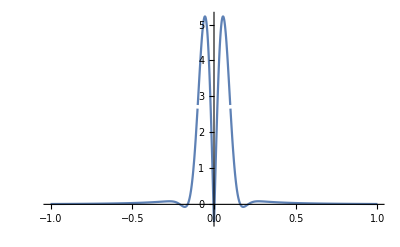

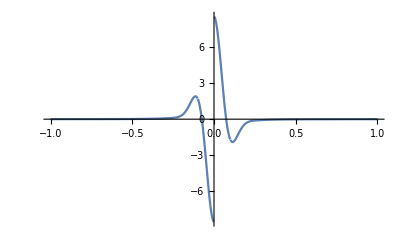

```mathematica
E^(-D(a+I uν)^2)ExpIntegralEi[D(a+I uν)^2]/.D->100/.uν->0.1//N
Plot[Re[%],{a,-1,1},PlotRange->All]
Plot[Im[%%],{a,-1,1},PlotRange->All]
```

```mathematica
"Can we derive this result analytically?"
(E^(- D ζ^2))/(a + uν I + ζ)/.ζ->ζ - (a + uν I )
-(E^(- D ζ^2))/(a + uν I - ζ)/.ζ->ζ + (a + uν I )
HoldForm[Integrate[(ⅇ^(-D (a+ⅈ uν+ζ)^2))/ζ,{ζ,a + uν I,∞}]]
```

Can we derive this result analytically?

(ⅇ^(-D (-a-ⅈ uν+ζ)^2))/ζ

(ⅇ^(-D (a+ⅈ uν+ζ)^2))/ζ

∫_(a+uν ⅈ)^∞ (ⅇ^(-D (a+ⅈ uν+ζ)^2))/ζ ⅆζ

```mathematica
Assuming[z∈Complexes,Integrate[(ⅇ^(-D (ζ)^2))/ζ,{ζ,z,∞}]]
```

ConditionalExpression[1/2 Gamma[0,D z^2], Re[z]>0&&Im[z]==0&&Re[D]>0]

#### More kinematics

HeavisideTheta[q v-ω-(q^2 ℏ)/(2 mχ)] HeavisideTheta[q v+ω+(q^2 ℏ)/(2 mχ)]

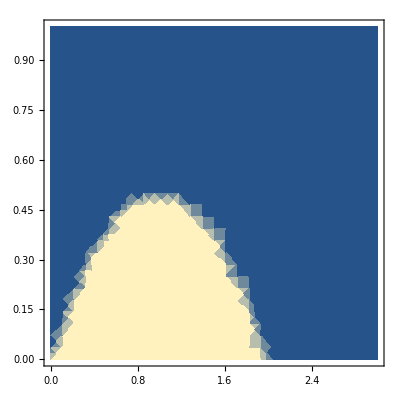

{{q→-(mχ (-v+(√(mχ v^2-2 ω ℏ))/(√mχ)))/ℏ},{q→(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ}}

HeavisideTheta[q+(mχ (-v+(√(mχ v^2-2 ω ℏ))/(√mχ)))/ℏ] HeavisideTheta[q-(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ]

```mathematica
HeavisideTheta[ωm-ω]HeavisideTheta[ωp+ω]/.ωm->q v - (ℏ q^2)/(2 mχ) /.ωp->q v + (ℏ q^2)/(2 mχ) 
DensityPlot[%/.ℏ->1/.mχ->1/.v->1,{q,0,3},{ω,0,1}]
Solve[q v-ω-(q^2 ℏ)/(2 mχ)==0,q]
HeavisideTheta[q-(q/.%[[1]])]HeavisideTheta[q-(q/.%[[2]])]
```

HeavisideTheta[q v-ω-(q^2 ℏ)/(2 mχ)] HeavisideTheta[q v+ω+(q^2 ℏ)/(2 mχ)]

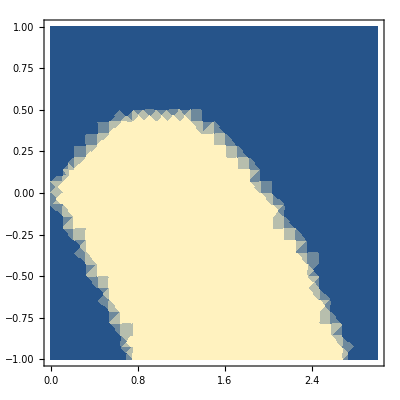

```mathematica
HeavisideTheta[q v-ω-(q^2 ℏ)/(2 mχ)]HeavisideTheta[q v+ω+(q^2 ℏ)/(2 mχ)](*HeavisideTheta[1/2 mχ v^2 +ω ℏ]*)
DensityPlot[%/.ℏ->1/.mχ->1/.v->1,{q,0,3},{ω,-1,1}]
```

(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ

(-mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ

HeavisideTheta[q-(-mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ] HeavisideTheta[-q+(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ]

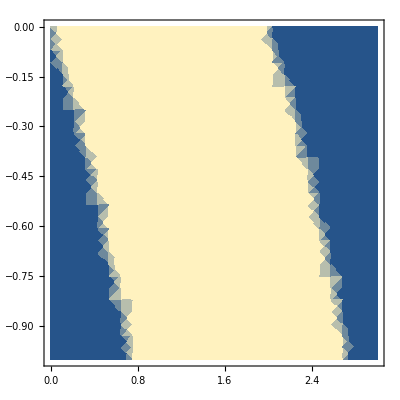

```mathematica
qp=q/.Solve[q v-ω-(q^2 ℏ)/(2 mχ)==0,q][[2]]//Simplify
mqm = q /.Solve[q v+ω+(q^2 ℏ)/(2 mχ)==0,q][[2]]//Simplify
HeavisideTheta[qp-q]HeavisideTheta[q-mqm]
DensityPlot[%/.ℏ->1/.mχ->1/.v->1,{q,0,3},{ω,-1,0}]
```

```mathematica
mqm/.ω->-Abs[ω]
D[%,ω]
```

(-mχ v+√mχ √(mχ v^2+2 ℏ Abs[ω]))/ℏ

(√mχ Abs'[ω])/(√(mχ v^2+2 ℏ Abs[ω]))

```mathematica
Clear[Absωsol]
Solve[(mqm/(2 kF)/.ω->-Abs[ω])==1/D,Abs[ω]]
Absωsol=(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)
(*Solve[(mqm/(2 kF))==1/D,ω]*)
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{Abs[ω]→(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)}}

(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)

```mathematica
Solve[(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)==mχ/(2 ℏ)(vesc^2-v^2),v]//Simplify
```

{{v→-vesc-(2 kF ℏ)/(D mχ)},{v→vesc-(2 kF ℏ)/(D mχ)}}

```mathematica
D[-mχ/(2 ℏ)(vesc^2-v^2)+(2 (D kF mχ v-kF^2 ℏ))/(D^2 mχ),v]
Solve[%==0,v]
```

(2 kF)/D+(mχ v)/ℏ

{{v→-(2 kF ℏ)/(D mχ)}}

{ℏ→1,D→300,mχ→1,kF→10,vesc→1}

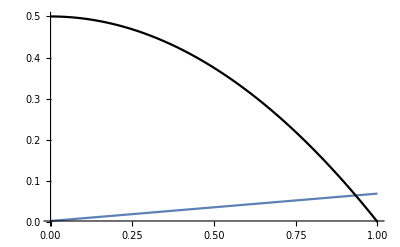

1/15

1

```mathematica
{ℏ->1,D->300,mχ->1,kF->10,vesc->1}
Show[{Plot[(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)/.%,{v,0,1},PlotRange->All],
Plot[mχ/(2 ℏ)(vesc^2-v^2)/.%,{v,0,1},PlotStyle->Black]}]
(2kF ℏ)/(D mχ)/.%%
vesc /.%%%
```

```mathematica
"D"/.FeTotalparams
```

{322.436,485.073,837.295,3156.08,81222.,1.70758×10^6}

```mathematica
("ℏ""qF""c")/("JpereV""D")/.SIConstRepl/.FeTotalparams
```

{8.90855,7.26316,5.52827,2.84744,0.561296,0.122416}

```mathematica
"vF"/.FeTotalparams
```

{1.68373×10^6,2.06517×10^6,2.71326×10^6,5.26776×10^6,2.67232×10^7,1.2253×10^8}

```mathematica
"Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution."
Drescale = "D"->("D")/b/.b->1
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[SiO2Totalparams]}]},{m,6,15}]
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[MgOTotalparams]}]},{m,6,15}]
"The lowest rescaling we can do where evaporation is still 0 is b=4"
Drescale = "D"->("D")/b/.b->4
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]
"The first rescaling where it is non-zero is b=5"
Drescale = "D"->("D")/b/.b->5
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
"This tells us that the energy threshold is less than ωedgei for most of the oscillators we consider. The conduction band of iron is the lowest, and only begins to contribute to the rate between b of 4-5 so about an additional suppression of 10^-4, and only for electron mass aDM "
Drescale = "D"->("D")/b/.b->8
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]
"So we need this much suppression to get contributions from higher masses"
```

Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution.

D→D

6 | 6.68936×10^6
76230.9
5.40093×10^6
5.25583×10^6
1.91904×10^11
8.86771×10^12
7 | 6.69176×10^6
78191.9
5.40243×10^6
5.2566×10^6
1.91904×10^11
8.86771×10^12
8 | 6.69201×10^6
78388.
5.40258×10^6
5.25668×10^6
1.91904×10^11
8.86771×10^12
9 | 6.69203×10^6
78407.6
5.40259×10^6
5.25669×10^6
1.91904×10^11
8.86771×10^12
10 | 6.69203×10^6
78409.6
5.40259×10^6
5.25669×10^6
1.91904×10^11
8.86771×10^12
11 | 6.69203×10^6
78409.8
5.40259×10^6
5.25669×10^6
1.91904×10^11
8.86771×10^12
12 | 6.69203×10^6
78409.8
5.40259×10^6
5.25669×10^6
1.91904×10^11
8.86771×10^12
13 | 6.69203×10^6
78409.8
5.40259×10^6
5.25669×10^6
1.91904×10^11
8.86771×10^12
14 | 6.69203×10^6
78409.8
5.40259×10^6
5.25669×10^6
1.91904×10^11
8.86771×10^12
15 | 6.69203×10^6
78409.8
5.40259×10^6
5.25669×10^6
1.91904×10^11
8.86771×10^12

{{6,{2.36298×10^8,4.02543×10^8}},{7,{2.36299×10^8,4.02543×10^8}},{8,{2.36299×10^8,4.02544×10^8}},{9,{2.36299×10^8,4.02544×10^8}},{10,{2.36299×10^8,4.02544×10^8}},{11,{2.36299×10^8,4.02544×10^8}},{12,{2.36299×10^8,4.02544×10^8}},{13,{2.36299×10^8,4.02544×10^8}},{14,{2.36299×10^8,4.02544×10^8}},{15,{2.36299×10^8,4.02544×10^8}}}

{{6,{1.48025×10^8,1.97675×10^8,2.11295×10^8,3.26826×10^8}},{7,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{8,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{9,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{10,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{11,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{12,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{13,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{14,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{15,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}}}

The lowest rescaling we can do where evaporation is still 0 is b=4

D→D/4

{{6,{1.65392×10^6,2486.66,1.33561×10^6,1.30235×10^6,4.7976×10^10,2.21693×10^12}},{7,{1.66354×10^6,10330.9,1.34158×10^6,1.30543×10^6,4.7976×10^10,2.21693×10^12}},{8,{1.6645×10^6,11115.3,1.34218×10^6,1.30574×10^6,4.7976×10^10,2.21693×10^12}},{9,{1.6646×10^6,11193.7,1.34224×10^6,1.30577×10^6,4.7976×10^10,2.21693×10^12}},{10,{1.66461×10^6,11201.6,1.34225×10^6,1.30577×10^6,4.7976×10^10,2.21693×10^12}},{11,{1.66461×10^6,11202.4,1.34225×10^6,1.30577×10^6,4.7976×10^10,2.21693×10^12}},{12,{1.66461×10^6,11202.4,1.34225×10^6,1.30577×10^6,4.7976×10^10,2.21693×10^12}},{13,{1.66461×10^6,11202.4,1.34225×10^6,1.30577×10^6,4.7976×10^10,2.21693×10^12}},{14,{1.66461×10^6,11202.4,1.34225×10^6,1.30577×10^6,4.7976×10^10,2.21693×10^12}},{15,{1.66461×10^6,11202.4,1.34225×10^6,1.30577×10^6,4.7976×10^10,2.21693×10^12}}}

The first rescaling where it is non-zero is b=5

D→D/5

6 | 1.31608×10^6
-4172.78
1.06327×10^6
1.03811×10^6
3.83808×10^10
1.77354×10^12
7 | 1.32811×10^6
5632.49
1.07073×10^6
1.04195×10^6
3.83808×10^10
1.77354×10^12
8 | 1.32931×10^6
6613.01
1.07148×10^6
1.04233×10^6
3.83808×10^10
1.77354×10^12
9 | 1.32943×10^6
6711.06
1.07155×10^6
1.04237×10^6
3.83808×10^10
1.77354×10^12
10 | 1.32945×10^6
6720.87
1.07156×10^6
1.04238×10^6
3.83808×10^10
1.77354×10^12
11 | 1.32945×10^6
6721.85
1.07156×10^6
1.04238×10^6
3.83808×10^10
1.77354×10^12
12 | 1.32945×10^6
6721.95
1.07156×10^6
1.04238×10^6
3.83808×10^10
1.77354×10^12
13 | 1.32945×10^6
6721.96
1.07156×10^6
1.04238×10^6
3.83808×10^10
1.77354×10^12
14 | 1.32945×10^6
6721.96
1.07156×10^6
1.04238×10^6
3.83808×10^10
1.77354×10^12
15 | 1.32945×10^6
6721.96
1.07156×10^6
1.04238×10^6
3.83808×10^10
1.77354×10^12

This tells us that the energy threshold is less than ωedgei for most of the oscillators we consider. The conduction band of iron is the lowest, and only begins to contribute to the rate between b of 4-5 so about an additional suppression of 10^-4, and only for electron mass aDM

D→D/8

{{6,{805323.,-17430.4,652256.,640452.,2.3988×10^10,1.10846×10^12}},{7,{824566.,-1741.93,664197.,646602.,2.3988×10^10,1.10846×10^12}},{8,{826490.,-173.091,665392.,647217.,2.3988×10^10,1.10846×10^12}},{9,{826683.,-16.2068,665511.,647279.,2.3988×10^10,1.10846×10^12}},{10,{826702.,-0.518387,665523.,647285.,2.3988×10^10,1.10846×10^12}},{11,{826704.,1.05045,665524.,647286.,2.3988×10^10,1.10846×10^12}},{12,{826704.,1.20734,665524.,647286.,2.3988×10^10,1.10846×10^12}},{13,{826704.,1.22303,665524.,647286.,2.3988×10^10,1.10846×10^12}},{14,{826704.,1.2246,665524.,647286.,2.3988×10^10,1.10846×10^12}},{15,{826704.,1.22475,665524.,647286.,2.3988×10^10,1.10846×10^12}}}

So we need this much suppression to get contributions from higher masses

```mathematica
"same as above, but for the raw kinematic constraint"
Drescale = "D"->("D")/b/.b->1
Table[{m,Table[-(2 "ℏ""qF")/("D" mχ)/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[-(2 "ℏ""qF")/("D" mχ)/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,{i,Length[SiO2Totalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[-(2 "ℏ""qF")/("D" mχ)/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,{i,Length[MgOTotalparams]}]},{m,6,15}]//TableForm
```

same as above, but for the raw kinematic constraint

D→D

6 | -5345.13
-4357.89
-3316.96
-1708.47
-336.778
-73.4496
7 | -534.513
-435.789
-331.696
-170.847
-33.6778
-7.34496
8 | -53.4513
-43.5789
-33.1696
-17.0847
-3.36778
-0.734496
9 | -5.34513
-4.35789
-3.31696
-1.70847
-0.336778
-0.0734496
10 | -0.534513
-0.435789
-0.331696
-0.170847
-0.0336778
-0.00734496
11 | -0.0534513
-0.0435789
-0.0331696
-0.0170847
-0.00336778
-0.000734496
12 | -0.00534513
-0.00435789
-0.00331696
-0.00170847
-0.000336778
-0.0000734496
13 | -0.000534513
-0.000435789
-0.000331696
-0.000170847
-0.0000336778
-7.34496×10^-6
14 | -0.0000534513
-0.0000435789
-0.0000331696
-0.0000170847
-3.36778×10^-6
-7.34496×10^-7
15 | -5.34513×10^-6
-4.35789×10^-6
-3.31696×10^-6
-1.70847×10^-6
-3.36778×10^-7
-7.34496×10^-8

6 | -3389.61
-1989.79
7 | -338.961
-198.979
8 | -33.8961
-19.8979
9 | -3.38961
-1.98979
10 | -0.338961
-0.198979
11 | -0.0338961
-0.0198979
12 | -0.00338961
-0.00198979
13 | -0.000338961
-0.000198979
14 | -0.0000338961
-0.0000198979
15 | -3.38961×10^-6
-1.98979×10^-6

6 | -4723.78
-3537.39
-3309.38
-2139.59
7 | -472.378
-353.739
-330.938
-213.959
8 | -47.2378
-35.3739
-33.0938
-21.3959
9 | -4.72378
-3.53739
-3.30938
-2.13959
10 | -0.472378
-0.353739
-0.330938
-0.213959
11 | -0.0472378
-0.0353739
-0.0330938
-0.0213959
12 | -0.00472378
-0.00353739
-0.00330938
-0.00213959
13 | -0.000472378
-0.000353739
-0.000330938
-0.000213959
14 | -0.0000472378
-0.0000353739
-0.0000330938
-0.0000213959
15 | -4.72378×10^-6
-3.53739×10^-6
-3.30938×10^-6
-2.13959×10^-6

```mathematica
"What is the minimum velocity for evaporation we can have if we ignored the fermi suppression?"
mχ/2(("vesc")^2-vχ^2)=="EF"
Solve[%,vχ][[2]]
Table[{m,%/.FeTotalparams/.Constants`EarthRepl/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl//Simplify},{m,6,15}]
"imaginary part implies EF is more than enough to evaporate at any velocity"
```

What is the minimum velocity for evaporation we can have if we ignored the fermi suppression?

1/2 mχ (vesc^2-vχ^2)==EF

{vχ→(√(-2 EF+vesc^2 mχ))/(√mχ)}

{{6,{{vχ→0.+1.20449×10^6 ⅈ},{vχ→0.+1.47738×10^6 ⅈ},{vχ→0.+1.94103×10^6 ⅈ},{vχ→0.+3.76854×10^6 ⅈ},{vχ→0.+1.91178×10^7 ⅈ},{vχ→0.+8.76579×10^7 ⅈ}}},{7,{{vχ→0.+380745. ⅈ},{vχ→0.+467067. ⅈ},{vχ→0.+613716. ⅈ},{vχ→0.+1.19167×10^6 ⅈ},{vχ→0.+6.04557×10^6 ⅈ},{vχ→0.+2.77199×10^7 ⅈ}}},{8,{{vχ→0.+119933. ⅈ},{vχ→0.+147317. ⅈ},{vχ→0.+193783. ⅈ},{vχ→0.+376689. ⅈ},{vχ→0.+1.91175×10^6 ⅈ},{vχ→0.+8.76579×10^6 ⅈ}}},{9,{{vχ→0.+36407.2 ⅈ},{vχ→0.+45357.8 ⅈ},{vχ→0.+60351.4 ⅈ},{vχ→0.+118645. ⅈ},{vχ→0.+604454. ⅈ},{vχ→0.+2.77196×10^6 ⅈ}}},{10,{{vχ→0.+4433.12 ⅈ},{vχ→0.+9635.21 ⅈ},{vχ→0.+15853.5 ⅈ},{vχ→0.+35982.8 ⅈ},{vχ→0.+190850. ⅈ},{vχ→0.+876508. ⅈ}}},{11,{{vχ→10532.4},{vχ→10179.},{vχ→9368.17},{vχ→0.+4071.86 ⅈ},{vχ→0.+59409.3 ⅈ},{vχ→0.+276972. ⅈ}}},{12,{{vχ→11135.},{vχ→11102.1},{vχ→11030.5},{vχ→10546.9},{vχ→0.+15493.5 ⅈ},{vχ→0.+86939.5 ⅈ}}},{13,{{vχ→11193.5},{vχ→11190.3},{vχ→11183.2},{vχ→11136.4},{vχ→9428.2},{vχ→0.+25356.5 ⅈ}}},{14,{{vχ→11199.4},{vχ→11199.},{vχ→11198.3},{vχ→11193.7},{vχ→11035.6},{vχ→6971.43}}},{15,{{vχ→11199.9},{vχ→11199.9},{vχ→11199.8},{vχ→11199.4},{vχ→11183.7},{vχ→10851.5}}}}

imaginary part implies EF is more than enough to evaporate at any velocity

### Mermin Limit to lindhard

#### Limits of Arctan to match onto the Heaviside

```mathematica
Assuming[0<a<1,Limit[ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ],uτ->∞]]
Assuming[1<a,Limit[ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ],uτ->∞]]
Assuming[a<0,Limit[ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ],uτ->∞]]
```

π

0

Piecewise[{{π, a≥-1}, {0, True}}]

```mathematica
Limit[ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ],uτ->∞]
%/.a->1/2
%%/.a->2
%%%/.a->-2
```

(√((-1+a)^2) π)/(2-2 a)+(√((1+a)^2) π)/(2+2 a)

π

0

0

```mathematica
Assuming[0<a<1,(√((-1+a)^2) π)/(2-2 a)+(√((1+a)^2) π)/(2+2 a)//Simplify]
Assuming[1<a,(√((-1+a)^2) π)/(2-2 a)+(√((1+a)^2) π)/(2+2 a)//Simplify]
Assuming[a<0,(√((-1+a)^2) π)/(2-2 a)+(√((1+a)^2) π)/(2+2 a)//Simplify]
```

π

0

Piecewise[{{π, a≥-1}, {0, True}}]

```mathematica
Assuming[0<a<1,π HeavisideTheta[1-Abs[a]]//Simplify]
Assuming[1<a,π HeavisideTheta[1-Abs[a]]//Simplify]
Assuming[a<0,π HeavisideTheta[1-Abs[a]]//Simplify]
```

π

0

π HeavisideTheta[1+a]

This shows how we match the complex part of the Mermin dielectric onto the Lindhard dielectric. We have simply that

```mathematica
HoldForm@(-Limit[(ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ]),uτ->∞] ==-π HeavisideTheta[1-Abs[a]]) (*Subscript[h, 1]*)
```

-lim_(uτ→∞) (ArcTan[(1+a) uτ]+ArcTan[(1-a) uτ])==-π HeavisideTheta[1-Abs[a]]

#### Mermin to Lindhard Z limits

```mathematica
ReZ=a + 1/2(1-a^2)Log[(1+a)/(1-a)] ;(*Re Z*)
ReϵM=1+1/(4z)((ReZ/.a->u+z)-(ReZ/.a->u-z))
```

1+1/(4 z)(2 z-1/2 (1-(u-z)^2) Log[(1+u-z)/(1-u+z)]+1/2 (1-(u+z)^2) Log[(1+u+z)/(1-u-z)])

```mathematica
ImZ=- I 1/2(1-a^2)π HeavisideTheta[1 - a];(*Im Z*)
ImϵM=1/(4z)((ImZ/.a->u+z)-(ImZ/.a->u-z));
Print["If u+z<1: \n",Assuming[u-z<1&&u+z<1,ImϵM//Simplify]]
Print["If u-z<1<u+z: \n",Assuming[u-z<1<u+z,ImϵM//Simplify]]
Print["If 1<u-z: \n",Assuming[1<u-z&&1<u+z,ImϵM//Simplify]]
```

If u+z<1: 
(ⅈ π u)/2

If u-z<1<u+z: 
-(ⅈ π (-1+u^2-2 u z+z^2))/(8 z)

If 1<u-z: 
0

### Mermin Analytics

#### As in the notes

```mathematica
Integrate[ζ Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)],{ζ,0,1},Assumptions->{{a,uν}∈ Reals,uν!=0}]
```

2 a (1+uν ArcTan[(-1+a)/uν]-uν ArcTan[(1+a)/uν])+(1-a^2+uν^2) ArcTanh[(2 a)/(1+a^2+uν^2)]

```mathematica
Integrate[ζ ArcTan[(a+ζ)/uν],{ζ,0,1},Assumptions->{{a,uν}∈ Reals}]
```

ConditionalExpression[1/2 (ArcTan[(1+a)/uν]+(-a^2+uν^2) ArcTan[uν/a]+(a-uν) (a+uν) ArcTan[uν/(1+a)]+uν (-1-a Log[a^2+uν^2]+a Log[(1+a)^2+uν^2])), a>0||a<-1]

```mathematica
-Integrate[(ζ-Abs[a]) ArcTan[ζ/uν],{ζ,Abs[a]-1,Abs[a]+1},Assumptions->{{a,uν}∈ Reals}]//Normal//Simplify//TrigToExp//FullSimplify;
Assuming[a∈Reals&&a>0,%//Simplify//PowerExpand//FullSimplify]
```

1/2 (2 uν+a^2 ArcTan[(1-a)/uν]+(1+uν^2) ArcTan[(-1+a)/uν]+(-1+a^2-uν^2) ArcTan[(1+a)/uν]-2 a uν ArcTanh[(2 a)/(1+a^2+uν^2)])

```mathematica
ArcTanh[(2 a)/(1+a^2+uν^2)]//TrigToExp//PowerExpand
```

-1/2 Log[1-(2 a)/(1+a^2+uν^2)]+1/2 Log[1+(2 a)/(1+a^2+uν^2)]

```mathematica
"check a higher moment too"
Integrate[ζ^2 Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)],{ζ,0,1},Assumptions->{{a,uν}∈ Reals,uν!=0}]
```

check a higher moment too

1/3 (2 a+(6 a^2 uν-2 uν^3) ArcTan[(-1+a)/uν]+4 uν (-3 a^2+uν^2) ArcTan[a/uν]+6 a^2 uν ArcTan[(1+a)/uν]-2 uν^3 ArcTan[(1+a)/uν]-Log[(-1+a)^2+uν^2]+a^3 Log[(-1+a)^2+uν^2]-3 a uν^2 Log[(-1+a)^2+uν^2]-2 a^3 Log[a^2+uν^2]+6 a uν^2 Log[a^2+uν^2]+(1+a^3-3 a uν^2) Log[(1+a)^2+uν^2])

#### Use the Integration by parts method - non-Degenerate Case

```mathematica
(*"Non-degenerate case"
Integrate[E^(-D ζ^2)(1/(a + I uν - ζ)-1/(a + I uν + ζ)),{ζ,0,∞},Assumptions->{{a,uν,D}∈Reals,{D,uν}>0}]//Simplify//PowerExpand//FullSimplify*)
```

Non-degenerate case

ⅇ^(-D (a+ⅈ uν)^2) (-ⅈ π+ExpIntegralEi[D (a+ⅈ uν)^2])

```mathematica
"non-degenerate case"
-Integrate[E^(-D ζ^2)(1/(a + I uν - ζ)+1/(a + I uν + ζ)),{ζ,0,∞},Assumptions->{{a,uν,D}∈Reals,{D,uν}>0}]//Simplify//PowerExpand//FullSimplify
"This is a dawson function!"
```

non-degenerate case

-ⅇ^(-D (a+ⅈ uν)^2) (π Erfi[√D (a+ⅈ uν)]+Log[-a-ⅈ uν]-Log[a+ⅈ uν])

This is a dawson function!

```mathematica
+Log[-a-ⅈ uν]-Log[a+ⅈ uν]//ComplexExpand
(*ArcTan[1+a+I uν]//ComplexExpand*)
- I(Log[a^2] + 2 ArcTan[uν/a])//ComplexExpand
```

ⅈ (Arg[-a-ⅈ uν]-Arg[a+ⅈ uν])

ⅈ (Arg[1-(ⅈ uν)/a]-Arg[1+(ⅈ uν)/a]-Log[a^2])

```mathematica
ComplexExpand[ArcTan[x+I]+ArcTan[x+I]]
```

-Arg[2-ⅈ x]+Arg[ⅈ x]+ⅈ (-1/2 Log[x^2]+1/2 Log[4+x^2])

```mathematica
"non-Degenerate case integral bulk"
"Real part"
ReBulk=Integrate[Integrate[ζ E^(-D ζ^2),ζ] Re[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify,ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(*(%/.ζ->1)-(%/.ζ->0)//FullSimplify*)
"Imaginary part"
ImBulk=Integrate[Integrate[ζ E^(-D ζ^2),ζ] Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify],ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
```

non-Degenerate case integral bulk

Real part

-1/D a Integrate[(ⅇ^(-D ζ^2) (a^2+uν^2-ζ^2))/((a^2+uν^2-2 a ζ+ζ^2) (a^2+uν^2+2 a ζ+ζ^2)),ζ,Assumptions→(a|uν)∈ℝ&&uν>0]

Imaginary part

-1/(2 D)uν Integrate[ⅇ^(-D ζ^2) (-1/(uν^2+(a-ζ)^2)-1/(uν^2+(a+ζ)^2)),ζ,Assumptions→(a|uν)∈ℝ&&uν>0]

```mathematica
"non-degenerate case boundary term"
Integrate[ζ E^(-D ζ^2),ζ]Integrate[1/(a -w + I uν),{w,-ζ,ζ},Assumptions->{{a,uν}∈Reals,uν>0}]//Normal
Limit[%,ζ->0]
Limit[%,ζ->∞]
"So in the non-degenerate case, there is no boundary term"
```

non-degenerate case boundary term

-(ⅇ^(-D ζ^2) ArcTanh[ζ/(a+ⅈ uν)])/D

0

0

So in the non-degenerate case, there is no boundary term

```mathematica
Integrate[ζ E^(-D ζ^2),ζ]
```

-(ⅇ^(-D ζ^2))/(2 D)

```mathematica
"degenerate case boundary term"
"Real part"
ReBound =Integrate[ζ E^(-D ζ^2),ζ] Integrate[Re[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
"Imaginary part"
ImBound =Integrate[ζ E^(-D ζ^2),ζ] Integrate[Im[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
```

degenerate case boundary term

Real part

-(ⅇ^(-D ζ^2) Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)])/(4 D)

Imaginary part

-(ⅇ^(-D ζ^2) (ArcTan[(a-ζ)/uν]-ArcTan[(a+ζ)/uν]))/(2 D)

```mathematica
"Real part"
Limit[ReBound,ζ->∞,Assumptions->{{a,uν}∈Reals,{D,uν}>0}]
ReBound/.ζ->0
"Imaginary part"
Assuming[{a,uν}∈Reals&&D>0,Limit[ImBound,ζ->∞]]
ImBound/.ζ->0
```

Real part

ConditionalExpression[0, D>0]

0

Imaginary part

0

0

#### Integration by parts method - Degenerate case (and it’s moments)

```mathematica
"degenerate case boundary term"
"Real part"
ReBound = ζ^2/2 Integrate[Re[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(%/.ζ->1)-(%/.ζ->0)
"Imaginary part"
ImBound =ζ^2/2 Integrate[Im[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(%/.ζ->1)-(%/.ζ->0)
```

degenerate case boundary term

Real part

1/4 ζ^2 Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)]

1/4 Log[1+(4 a)/((-1+a)^2+uν^2)]

Imaginary part

1/2 ζ^2 (ArcTan[(a-ζ)/uν]-ArcTan[(a+ζ)/uν])

1/2 (ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν])

```mathematica
"Degenerate case integral bulk"
"Real part"
ReBulk=Integrate[Integrate[ζ ,ζ]Re[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify,ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(%/.ζ->1)-(%/.ζ->0)//FullSimplify
"Imaginary part"
ImBulk=Integrate[Integrate[ζ ,ζ]Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify],ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(%/.ζ->1)-(%/.ζ->0)//FullSimplify
```

Degenerate case integral bulk

Real part

-a ζ+a uν ArcTan[(-a+ζ)/uν]+a uν ArcTan[(a+ζ)/uν]+1/4 (-a^2+uν^2) Log[a^2+uν^2-2 a ζ+ζ^2]+1/4 (a^2-uν^2) Log[a^2+uν^2+2 a ζ+ζ^2]

-a+a uν ArcTan[(1-a)/uν]+a uν ArcTan[(1+a)/uν]-1/4 (a-uν) (a+uν) (Log[(-1+a)^2+uν^2]-Log[(1+a)^2+uν^2])

Imaginary part

1/2 uν (-2 ζ+(-a^2/uν+uν) ArcTan[(-a+ζ)/uν]+(-a^2/uν+uν) ArcTan[(a+ζ)/uν]-a Log[a^2+uν^2-2 a ζ+ζ^2]+a Log[a^2+uν^2+2 a ζ+ζ^2])

1/2 ((a-uν) (a+uν) ArcTan[(-1+a)/uν]+(-a^2+uν^2) ArcTan[(1+a)/uν]+uν (-2-a Log[(-1+a)^2+uν^2]+a Log[(1+a)^2+uν^2]))

```mathematica
ReTotal = ReBound+ReBulk//FullSimplify
ImTotal = ImBound+ImBulk//FullSimplify
```

a uν ArcTan[(-a+ζ)/uν]+a uν ArcTan[(a+ζ)/uν]+1/4 ζ (-4 a+ζ Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)])-1/4 (a-uν) (a+uν) (Log[uν^2+(a-ζ)^2]-Log[uν^2+(a+ζ)^2])

1/2 ((a^2+ζ^2) ArcTan[(a-ζ)/uν]+uν (-2 ζ+uν ArcTan[(-a+ζ)/uν])-(a^2-uν^2+ζ^2) ArcTan[(a+ζ)/uν]+a uν (-Log[uν^2+(a-ζ)^2]+Log[uν^2+(a+ζ)^2]))

#### Perturbing away from degenerate case

```mathematica
ftilde =Integrate[ζ FOccnDζnearkF,ζ]
```

1/2 (ζ^2/2+(D ζ^2)/2-(D ζ^3)/3)

```mathematica
"degenerate case boundary term"
"Real part"
ReBound =ftilde Integrate[Re[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
"Imaginary part"
ImBound =ftilde Integrate[Im[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
```

degenerate case boundary term

Real part

1/4 (ζ^2/2+(D ζ^2)/2-(D ζ^3)/3) Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)]

Imaginary part

1/2 (ζ^2/2+(D ζ^2)/2-(D ζ^3)/3) (ArcTan[(a-ζ)/uν]-ArcTan[(a+ζ)/uν])

```mathematica
"Degenerate case integral bulk"
"Real part"
ReBulk=-Integrate[ftilde Re[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify,ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(*(%/.ζ->1)-(%/.ζ->0)//FullSimplify*)
"Imaginary part"
ImBulk=-Integrate[ftilde Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify],ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(*(%/.ζ->1)-(%/.ζ->0)//FullSimplify*)
```

Degenerate case integral bulk

Real part

1/24 (12 a (1+D) ζ-4 a D ζ^2-4 uν (-3 a^2 D+3 a (1+D)+D uν^2) ArcTan[(-a+ζ)/uν]-4 uν (3 a^2 D+3 a (1+D)-D uν^2) ArcTan[(a+ζ)/uν]+(-2 a^3 D+3 a^2 (1+D)+6 a D uν^2-3 (1+D) uν^2) Log[a^2+uν^2-2 a ζ+ζ^2]+(-2 a^3 D-3 a^2 (1+D)+6 a D uν^2+3 (1+D) uν^2) Log[a^2+uν^2+2 a ζ+ζ^2])

Imaginary part

-1/12 uν (-6 (1+D) ζ+2 D ζ^2+((2 a^3 D-3 a^2 (1+D)-6 a D uν^2+3 (1+D) uν^2) ArcTan[(-a+ζ)/uν])/uν+1/uν(-2 a^3 D-3 a^2 (1+D)+6 a D uν^2+3 (1+D) uν^2) ArcTan[(a+ζ)/uν]+(3 a^2 D-3 a (1+D)-D uν^2) Log[a^2+uν^2-2 a ζ+ζ^2]+(3 a^2 D+3 a (1+D)-D uν^2) Log[a^2+uν^2+2 a ζ+ζ^2])

```mathematica
ReTotal = ReBound+ReBulk//FullSimplify
ImTotal = ImBound+ImBulk//FullSimplify
```

1/24 (12 a (1+D) ζ-4 a D ζ^2+4 uν (-3 a^2 D+3 a (1+D)+D uν^2) ArcTan[(a-ζ)/uν]-4 uν (3 a (1+D+a D)-D uν^2) ArcTan[(a+ζ)/uν]+(-2 a^3 D+3 a^2 (1+D)+6 a D uν^2-3 (1+D) uν^2) Log[uν^2+(a-ζ)^2]+(3+D (3-2 ζ)) ζ^2 Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)]+(-a^2 (3+(3+2 a) D)+3 (1+D+2 a D) uν^2) Log[uν^2+(a+ζ)^2])

1/12 ((2 a^3 D-3 a^2 (1+D)-6 a D uν^2+3 (1+D) uν^2+ζ^2 (3+3 D-2 D ζ)) ArcTan[(a-ζ)/uν]+(2 a^3 D+3 a^2 (1+D)-6 a D uν^2-3 (1+D) uν^2+ζ^2 (-3-3 D+2 D ζ)) ArcTan[(a+ζ)/uν]+uν (2 ζ (3+3 D-D ζ)+(-3 a^2 D+3 a (1+D)+D uν^2) Log[uν^2+(a-ζ)^2]+(-3 a (1+D+a D)+D uν^2) Log[uν^2+(a+ζ)^2]))

```mathematica
ReTotalWbounds=(ReTotal/.ζ->1+1/D- 2 zt/D )-(ReTotal/.ζ->1-1/D )//Simplify;
ImTotalWbounds=(ImTotal/.ζ->1+1/D- 2 zt/D )-(ImTotal/.ζ->1-1/D )//Simplify;
```

```mathematica
Limit[ReTotalWbounds ,D->∞]
Limit[ImTotalWbounds ,D->∞]
```

0

0

```mathematica
Limit[ReTotalWbounds D,D->∞]
Limit[ImTotalWbounds D,D->∞]
```

-1/2 (-1+zt^2) Log[1+(4 a)/((-1+a)^2+uν^2)]

-1/2 ⅈ (-1+zt^2) (Log[1-(ⅈ (-1+a))/uν]-Log[1+(ⅈ (-1+a))/uν]-Log[1-(ⅈ (1+a))/uν]+Log[1+(ⅈ (1+a))/uν])

```mathematica
2 ArcTan[(#-1)/I]+Arg[2-#]&;
Assuming[{zt,z,uν}∈Reals,-1/2 ⅈ (-1+zt^2) (Log[1-(ⅈ (-1+a))/uν]-Log[1+(ⅈ (-1+a))/uν]-Log[1-(ⅈ (1+a))/uν]+Log[1+(ⅈ (1+a))/uν])//ComplexExpand//Simplify]
(-1+zt^2)(-ArcTan[(-1+a)/uν]+ArcTan[(1+a)/uν])
%//ComplexExpand//Simplify
```

1/2 (-1+zt^2) (Arg[1-(ⅈ (-1+a))/uν]-Arg[1+(ⅈ (-1+a))/uν]-Arg[1-(ⅈ (1+a))/uν]+Arg[1+(ⅈ (1+a))/uν])

(-1+zt^2) (-ArcTan[(-1+a)/uν]+ArcTan[(1+a)/uν])

1/2 (-1+zt^2) (Arg[1-(ⅈ (-1+a))/uν]-Arg[1+(ⅈ (-1+a))/uν]-Arg[1-(ⅈ (1+a))/uν]+Arg[1+(ⅈ (1+a))/uν])

```mathematica
ComplexExpand@ArcTan[x]
```

-1/2 Arg[1-ⅈ x]+1/2 Arg[1+ⅈ x]

```mathematica
2 ArcTan[(#-1)/I]+Arg[2-#]&
```

2 ArcTan[(#1-1)/ⅈ]+Arg[2-#1]&

#### ϵnd -> ϵnd_RPA(k,0)

```mathematica
Reh= 1/2 Log[(1+a)/(1-a)] ;(*Re h*)
Reϵnd=1+("χ")^2/(4 z^3)(1/("D")-z)((Reh/.a->u+z)-(Reh/.a->u-z))
%/.u->0//Simplify//PowerExpand
```

1+(χ^2 (1/D-z) (-1/2 Log[(1+u-z)/(1-u+z)]+1/2 Log[(1+u+z)/(1-u-z)]))/(4 z^3)

1+(χ^2 (-1+D z) (2 Log[1-z]-2 Log[1+z]))/(8 D z^3)

```mathematica
Imh=- I π HeavisideTheta[1 - Abs[a]];(*Im h*)
Imϵnd=("χ")^2/(4 z^3)(1/("D")-z)((Imh/.a->u+z)-(Imh/.a->u-z))/.u->0
Print["If z<1: \n",Assuming[-z<1&&z<1,Imϵnd//Simplify]]
Print["If -z<1<+z: \n",Assuming[-z<1<+z,Imϵnd//Simplify]]
(*Print["If 1<-z: \n",Assuming[1<-z&&1<+z,Imϵnd//Simplify]]*)
```

0

If z<1: 
0

If -z<1<+z: 
0

```mathematica
ϵnd0[z]
```

1+(χ^2 (1/D-z) Log[Abs[(1+z)/(1-z)]])/(2 z^3)

```mathematica
ϵRPA0[z]
```

1+(χ^2 (1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z)))/z^2

#### complex expression for h

```mathematica
Integrate[1/(a -w + I uν),{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
```

2 ArcTanh[ζ/(a+ⅈ uν)]

```mathematica
2 ArcTanh[ζ/(a+ⅈ uν)]//ComplexExpand//Simplify
```

1/2 (-2 ⅈ Arg[1-ζ/(a+ⅈ uν)]+2 ⅈ Arg[1+ζ/(a+ⅈ uν)]-Log[(a^2+uν^2-2 a ζ+ζ^2)/(a^2+uν^2)]+Log[(a^2+uν^2+2 a ζ+ζ^2)/(a^2+uν^2)])

#### compare ϵM to ϵMnd

```mathematica
Im[-1/ϵM[0.5,0.001,1]]/.{"χ"->1,"D"->300}
Im[-1/ϵMnd[0.5,0.001,1]]/.{"χ"->1,"D"->300}
```

1.79699×10^-6

0.000214148

```mathematica
ϵM[0.5,0.001,1]/.{"χ"->1,"D"->300}
ϵMnd[0.5,0.001,1]/.{"χ"->1,"D"->300}
```

106461.+535312. ⅈ

2154.85+1435.9 ⅈ

```mathematica
ϵM[0.5,0.001,1]Conjugate[ϵM[0.5,0.001,1]]/.{"χ"->1,"D"->300}
ϵMnd[0.5,0.001,1]Conjugate[ϵMnd[0.5,0.001,1]]/.{"χ"->1,"D"->300}
```

2.97893×10^11+0. ⅈ

6.70516×10^6+0. ⅈ

```mathematica
Im[-1/ϵM[0.5,0.001,1]]/.{"χ"->1,"D"->300}
Im[ϵMnd[0.5,0.001,1]/(ϵM[0.5,0.001,1]Conjugate[ϵM[0.5,0.001,1]])]/.{"χ"->1,"D"->300}
```

1.79699×10^-6

4.82017×10^-9

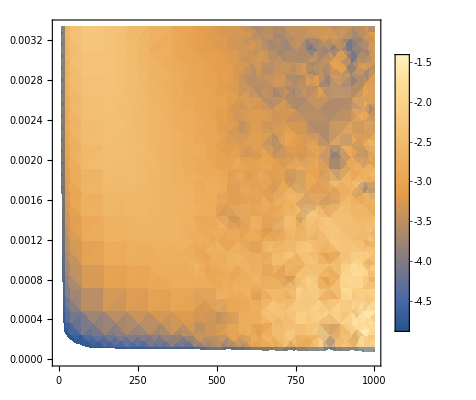

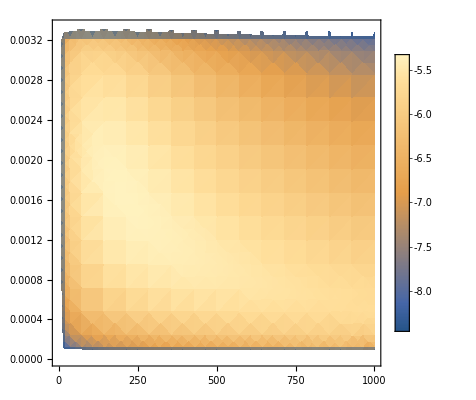

```mathematica
DensityPlot[Log10@Im[-1/ϵM[u,z,1]]/.{"χ"->1,"D"->300},{u,0,1000},{z,0,1/300},PlotLegends->Automatic]
DensityPlot[Log10@Im[ϵMnd[u,z,1]/(ϵM[u,z,1]Conjugate[ϵM[u,z,1]])]/.{"χ"->1,"D"->300},{u,0,1000},{z,0,1/300},PlotLegends->Automatic]
```

```mathematica
ϵM[0.5,0.001,1]Conjugate[ϵM[0.5,0.001,1]]/.{"χ"->1,"D"->300}
Abs[ϵM[0.5,0.001,1]]^2/.{"χ"->1,"D"->300}
```

2.97893×10^11+0. ⅈ

2.97893×10^11

### Cross-section and evaporation analytics for ϵnd

#### Integration bounds for dσ_nd dE_R

The integration bounds are given by the intersection of (0,1/D) and (z_-,z_+)

```mathematica
"if z_->1/D then the integral is 0 (region is empty)"
"if z_-<1/D<z_+ then the bounds are (z_-,1/D)"
"if z_+<1/D then the bounds are (z_-,z_+)"
"we want to summarize this with a single expression. We have a global factor of "
If[SubMinus[z]>=1/D,0,If[SubPlus[z]>1/D,"bounds are (z_-,1/D)", "bounds are (z_-,z_+)"]]
```

if z_->1/D then the integral is 0 (region is empty)

if z_-<1/D<z_+ then the bounds are (z_-,1/D)

if z_+<1/D then the bounds are (z_-,z_+)

we want to summarize this with a single expression. We have a global factor of

If[z_-≥1/D,0,If[z_+>1/D,bounds are (z_-,1/D),bounds are (z_-,z_+)]]

#### Evaporation distribution and bounds

```mathematica
"figure out the modification of the integrand needed to go from f_MB -> f_nd for the target"
fMBnorm = Assuming[βE mT/2 vT^2>0,Integrate[vT^2 E^(-βE mT/2 vT^2),{vT,0,∞}]]
FOccnDζnearkF/.ζ->(m vT)/(ℏ kF)
fndnorm =  Assuming[,Integrate[vT^2%,{vT,(m/(ℏ kF))^-1(1-1/D),(m/(ℏ kF))^-1(1+1/D)}]]//Simplify
```

figure out the modification of the integrand needed to go from f_MB -> f_nd for the target

(√(π/2))/(mT βE)^(3/2)

1/2 (1+D-(D m vT)/(kF ℏ))

((1-2 D+3 D^2) kF^3 ℏ^3)/(3 D^3 m^3)

#### ω st z integral returns 0

```mathematica
1/("D")==(mχ vχ- √(2 mχ (1/2 mχ vχ^2-ω ℏ)))/(2 kF ℏ)
Solve[%,ω]//Simplify
Solve[%%,vχ]//Simplify
```

1/D==(mχ vχ-√2 √(mχ ((mχ vχ^2)/2-ω ℏ)))/(2 kF ℏ)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ω→(2 kF (D mχ vχ-kF ℏ))/(D^2 mχ)}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{vχ→(D ω)/(2 kF)+(kF ℏ)/(D mχ)}}

```mathematica
AbsoluteTiming[Integrate[x,x]]
```

{0.0066989,x^2/2}

```mathematica
Monitor[Do[Pause[1],{i,10},{j,10}],{i,j}]
```

$Aborted

```mathematica
(mχ vχ- √(2 mχ (1/2 mχ vχ^2-ω ℏ)))/(2 kF ℏ)
D[%,vχ]//FullSimplify
"Derivative of RHS wrt vχ is negative"
D[%%%,ω]//FullSimplify
"Derivative of RHS wrt ω is positive"
```

(mχ vχ-√2 √(mχ ((mχ vχ^2)/2-ω ℏ)))/(2 kF ℏ)

(mχ (2-(2 mχ vχ)/(√(mχ (mχ vχ^2-2 ω ℏ)))))/(4 kF ℏ)

Derivative of RHS wrt vχ is negative

mχ/(2 kF √(mχ (mχ vχ^2-2 ω ℏ)))

Derivative of RHS wrt ω is positive

#### More kinematics

```mathematica
HeavisideTheta[ωm-ω]HeavisideTheta[ωp+ω]/.ωm->q v - (ℏ q^2)/(2 mχ) /.ωp->q v + (ℏ q^2)/(2 mχ) 
DensityPlot[%/.ℏ->1/.mχ->1/.v->1,{q,0,3},{ω,0,1}]
Solve[q v-ω-(q^2 ℏ)/(2 mχ)==0,q]
HeavisideTheta[q-(q/.%[[1]])]HeavisideTheta[q-(q/.%[[2]])]
```

HeavisideTheta[q v-ω-(q^2 ℏ)/(2 mχ)] HeavisideTheta[q v+ω+(q^2 ℏ)/(2 mχ)]

-Graphics-

{{q→-(mχ (-v+(√(mχ v^2-2 ω ℏ))/(√mχ)))/ℏ},{q→(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ}}

HeavisideTheta[q+(mχ (-v+(√(mχ v^2-2 ω ℏ))/(√mχ)))/ℏ] HeavisideTheta[q-(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ]

```mathematica
HeavisideTheta[q v-ω-(q^2 ℏ)/(2 mχ)]HeavisideTheta[q v+ω+(q^2 ℏ)/(2 mχ)](*HeavisideTheta[1/2 mχ v^2 +ω ℏ]*)
DensityPlot[%/.ℏ->1/.mχ->1/.v->1,{q,0,3},{ω,-1,1}]
```

HeavisideTheta[q v-ω-(q^2 ℏ)/(2 mχ)] HeavisideTheta[q v+ω+(q^2 ℏ)/(2 mχ)]

-Graphics-

```mathematica
qp=q/.Solve[q v-ω-(q^2 ℏ)/(2 mχ)==0,q][[2]]//Simplify
mqm = q /.Solve[q v+ω+(q^2 ℏ)/(2 mχ)==0,q][[2]]//Simplify
HeavisideTheta[qp-q]HeavisideTheta[q-mqm]
DensityPlot[%/.ℏ->1/.mχ->1/.v->1,{q,0,3},{ω,-1,0}]
```

(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ

(-mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ

HeavisideTheta[q-(-mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ] HeavisideTheta[-q+(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ]

-Graphics-

```mathematica
mqm/.ω->-Abs[ω]
D[%,ω]
```

(-mχ v+√mχ √(mχ v^2+2 ℏ Abs[ω]))/ℏ

(√mχ Abs'[ω])/(√(mχ v^2+2 ℏ Abs[ω]))

```mathematica
Clear[Absωsol]
Solve[(mqm/(2 kF)/.ω->-Abs[ω])==1/D,Abs[ω]]
Absωsol=(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)
(*Solve[(mqm/(2 kF))==1/D,ω]*)
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{Abs[ω]→(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)}}

(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)

```mathematica
Solve[(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)==mχ/(2 ℏ)(vesc^2-v^2),v]//Simplify
```

{{v→-vesc-(2 kF ℏ)/(D mχ)},{v→vesc-(2 kF ℏ)/(D mχ)}}

```mathematica
D[-mχ/(2 ℏ)(vesc^2-v^2)+(2 (D kF mχ v-kF^2 ℏ))/(D^2 mχ),v]
Solve[%==0,v]
```

(2 kF)/D+(mχ v)/ℏ

{{v→-(2 kF ℏ)/(D mχ)}}

```mathematica
{ℏ->1,D->300,mχ->1,kF->10,vesc->1}
Show[{Plot[(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)/.%,{v,0,1},PlotRange->All],
Plot[mχ/(2 ℏ)(vesc^2-v^2)/.%,{v,0,1},PlotStyle->Black]}]
(2kF ℏ)/(D mχ)/.%%
vesc /.%%%
```

{ℏ→1,D→300,mχ→1,kF→10,vesc→1}

-Graphics-

1/15

1

```mathematica
"D"/.FeTotalparams
```

{322.436,485.073,837.295,3156.08,81222.,1.70758×10^6}

```mathematica
("ℏ""qF""c")/("JpereV""D")/.SIConstRepl/.FeTotalparams
```

{8.90855,7.26316,5.52827,2.84744,0.561296,0.122416}

```mathematica
"vF"/.FeTotalparams
```

{1.68373×10^6,2.06517×10^6,2.71326×10^6,5.26776×10^6,2.67232×10^7,1.2253×10^8}

```mathematica
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
```

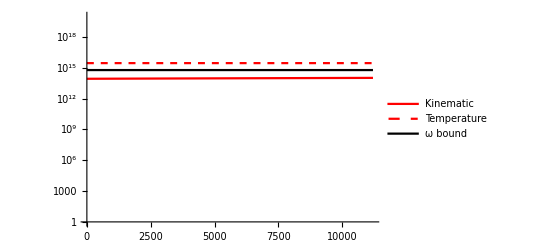

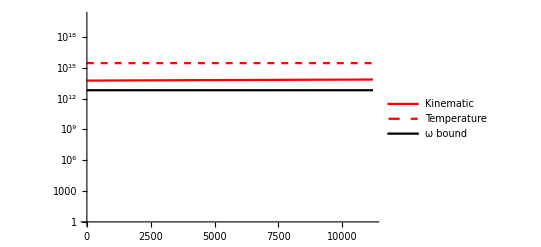

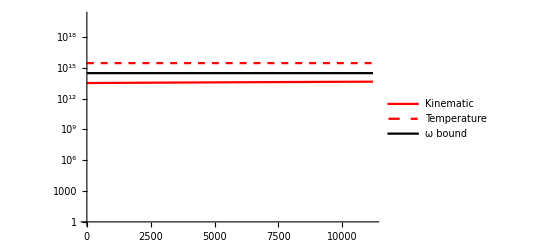

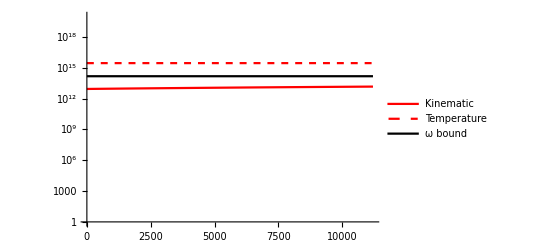

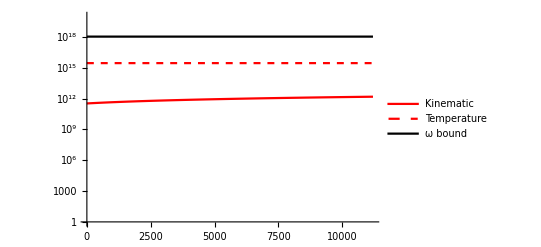

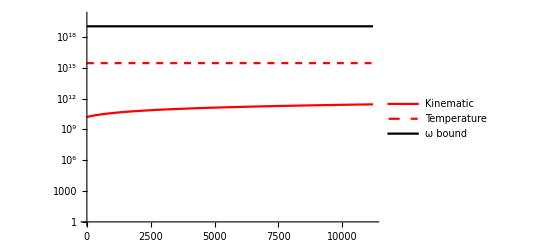

```mathematica
Do[Print@Show[{LogPlot[2 vχ ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.FeTotalparams[[o]]/.mχ->10^6("JpereV")/("c")^2/.SIConstRepl,{vχ,0,"vesc"/.EarthRepl},PlotStyle->Red,PlotRange->{10^0,10^20},PlotLegends->LineLegend[{Red,Directive[Red,Dashed],Black},{"Kinematic","Temperature","ω bound"}]],LogPlot[4/("β""ℏ")/.FeTotalparams[[o]],{vχ,0,"vesc"/.EarthRepl},PlotStyle->Directive[Red,Dashed]],LogPlot["ωedgei"/.FeTotalparams[[o]],{vχ,0,"vesc"/.EarthRepl},PlotStyle->Black]}],{o,Length[FeTotalparams]}]
```

```mathematica
"Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution."
Drescale = "D"->("D")/b/.b->1
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[SiO2Totalparams]}]},{m,6,15}]
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[MgOTotalparams]}]},{m,6,15}]
(*"The lowest rescaling we can do where evaporation is still 0 is b=4"
Drescale = "D"->("D")/b/.b->4
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]
"The first rescaling where it is non-zero is b=5"
Drescale = "D"->("D")/b/.b->5
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
"This tells us that the energy threshold is less than ωedgei for most of the oscillators we consider. The conduction band of iron is the lowest, and only begins to contribute to the rate between b of 4-5 so about an additional suppression of 10^-4, and only for electron mass aDM "
Drescale = "D"->("D")/b/.b->8
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]
"So we need this much suppression to get contributions from higher masses"*)
```

Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution.

D→D

6 | 293771.
-47548.7
244538.
251972.
1.01741×10^10
4.70135×10^11
7 | 339141.
-10559.2
272692.
266473.
1.01741×10^10
4.70135×10^11
8 | 343677.
-6860.2
275507.
267924.
1.01741×10^10
4.70135×10^11
9 | 344131.
-6490.31
275789.
268069.
1.01741×10^10
4.70135×10^11
10 | 344177.
-6453.32
275817.
268083.
1.01741×10^10
4.70135×10^11
11 | 344181.
-6449.62
275820.
268085.
1.01741×10^10
4.70135×10^11
12 | 344182.
-6449.25
275820.
268085.
1.01741×10^10
4.70135×10^11
13 | 344182.
-6449.21
275820.
268085.
1.01741×10^10
4.70135×10^11
14 | 344182.
-6449.21
275820.
268085.
1.01741×10^10
4.70135×10^11
15 | 344182.
-6449.21
275820.
268085.
1.01741×10^10
4.70135×10^11

{{6,{2.61001×10^7,4.44864×10^7}},{7,{2.61139×10^7,4.44945×10^7}},{8,{2.61152×10^7,4.44953×10^7}},{9,{2.61154×10^7,4.44954×10^7}},{10,{2.61154×10^7,4.44954×10^7}},{11,{2.61154×10^7,4.44954×10^7}},{12,{2.61154×10^7,4.44954×10^7}},{13,{2.61154×10^7,4.44954×10^7}},{14,{2.61154×10^7,4.44954×10^7}},{15,{2.61154×10^7,4.44954×10^7}}}

{{6,{1.63346×10^7,2.18293×10^7,2.33362×10^7,3.61145×10^7}},{7,{1.63538×10^7,2.18437×10^7,2.33496×10^7,3.61233×10^7}},{8,{1.63558×10^7,2.18451×10^7,2.3351×10^7,3.61241×10^7}},{9,{1.6356×10^7,2.18453×10^7,2.33511×10^7,3.61242×10^7}},{10,{1.6356×10^7,2.18453×10^7,2.33511×10^7,3.61242×10^7}},{11,{1.6356×10^7,2.18453×10^7,2.33511×10^7,3.61242×10^7}},{12,{1.6356×10^7,2.18453×10^7,2.33511×10^7,3.61242×10^7}},{13,{1.6356×10^7,2.18453×10^7,2.33511×10^7,3.61242×10^7}},{14,{1.6356×10^7,2.18453×10^7,2.33511×10^7,3.61242×10^7}},{15,{1.6356×10^7,2.18453×10^7,2.33511×10^7,3.61242×10^7}}}

```mathematica
"same as above, but for the raw kinematic constraint"
Drescale = "D"->("D")/b/.b->1
Table[{m,Table[-(2 "ℏ""qF")/("D" mχ)/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[-(2 "ℏ""qF")/("D" mχ)/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,{i,Length[SiO2Totalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[-(2 "ℏ""qF")/("D" mχ)/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,{i,Length[MgOTotalparams]}]},{m,6,15}]//TableForm
```

same as above, but for the raw kinematic constraint

D→D

6 | -100820.
-82198.9
-62564.8
-32225.2
-6352.32
-1385.41
7 | -10082.
-8219.89
-6256.48
-3222.52
-635.232
-138.541
8 | -1008.2
-821.989
-625.648
-322.252
-63.5232
-13.8541
9 | -100.82
-82.1989
-62.5648
-32.2252
-6.35232
-1.38541
10 | -10.082
-8.21989
-6.25648
-3.22252
-0.635232
-0.138541
11 | -1.0082
-0.821989
-0.625648
-0.322252
-0.0635232
-0.0138541
12 | -0.10082
-0.0821989
-0.0625648
-0.0322252
-0.00635232
-0.00138541
13 | -0.010082
-0.00821989
-0.00625648
-0.00322252
-0.000635232
-0.000138541
14 | -0.0010082
-0.000821989
-0.000625648
-0.000322252
-0.0000635232
-0.0000138541
15 | -0.00010082
-0.0000821989
-0.0000625648
-0.0000322252
-6.35232×10^-6
-1.38541×10^-6

6 | -30658.4
-17997.3
7 | -3065.84
-1799.73
8 | -306.584
-179.973
9 | -30.6584
-17.9973
10 | -3.06584
-1.79973
11 | -0.306584
-0.179973
12 | -0.0306584
-0.0179973
13 | -0.00306584
-0.00179973
14 | -0.000306584
-0.000179973
15 | -0.0000306584
-0.0000179973

6 | -42725.8
-31995.1
-29932.8
-19352.2
7 | -4272.58
-3199.51
-2993.28
-1935.22
8 | -427.258
-319.951
-299.328
-193.522
9 | -42.7258
-31.9951
-29.9328
-19.3522
10 | -4.27258
-3.19951
-2.99328
-1.93522
11 | -0.427258
-0.319951
-0.299328
-0.193522
12 | -0.0427258
-0.0319951
-0.0299328
-0.0193522
13 | -0.00427258
-0.00319951
-0.00299328
-0.00193522
14 | -0.000427258
-0.000319951
-0.000299328
-0.000193522
15 | -0.0000427258
-0.0000319951
-0.0000299328
-0.0000193522

```mathematica
"What is the minimum velocity for evaporation we can have if we ignored the fermi suppression?"
mχ/2(("vesc")^2-vχ^2)=="EF"
Solve[%,vχ][[2]]
Table[{m,%/.FeTotalparams/.Constants`EarthRepl/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl//Simplify},{m,6,15}]
"imaginary part implies EF is more than enough to evaporate at any velocity"
```

What is the minimum velocity for evaporation we can have if we ignored the fermi suppression?

1/2 mχ (vesc^2-vχ^2)==EF

{vχ→(√(-2 EF+vesc^2 mχ))/(√mχ)}

{{6,{{vχ→0.+1.20449×10^6 ⅈ},{vχ→0.+1.47738×10^6 ⅈ},{vχ→0.+1.94103×10^6 ⅈ},{vχ→0.+3.76854×10^6 ⅈ},{vχ→0.+1.91178×10^7 ⅈ},{vχ→0.+8.76579×10^7 ⅈ}}},{7,{{vχ→0.+380745. ⅈ},{vχ→0.+467067. ⅈ},{vχ→0.+613716. ⅈ},{vχ→0.+1.19167×10^6 ⅈ},{vχ→0.+6.04557×10^6 ⅈ},{vχ→0.+2.77199×10^7 ⅈ}}},{8,{{vχ→0.+119933. ⅈ},{vχ→0.+147317. ⅈ},{vχ→0.+193783. ⅈ},{vχ→0.+376689. ⅈ},{vχ→0.+1.91175×10^6 ⅈ},{vχ→0.+8.76579×10^6 ⅈ}}},{9,{{vχ→0.+36407.2 ⅈ},{vχ→0.+45357.8 ⅈ},{vχ→0.+60351.4 ⅈ},{vχ→0.+118645. ⅈ},{vχ→0.+604454. ⅈ},{vχ→0.+2.77196×10^6 ⅈ}}},{10,{{vχ→0.+4433.12 ⅈ},{vχ→0.+9635.21 ⅈ},{vχ→0.+15853.5 ⅈ},{vχ→0.+35982.8 ⅈ},{vχ→0.+190850. ⅈ},{vχ→0.+876508. ⅈ}}},{11,{{vχ→10532.4},{vχ→10179.},{vχ→9368.17},{vχ→0.+4071.86 ⅈ},{vχ→0.+59409.3 ⅈ},{vχ→0.+276972. ⅈ}}},{12,{{vχ→11135.},{vχ→11102.1},{vχ→11030.5},{vχ→10546.9},{vχ→0.+15493.5 ⅈ},{vχ→0.+86939.5 ⅈ}}},{13,{{vχ→11193.5},{vχ→11190.3},{vχ→11183.2},{vχ→11136.4},{vχ→9428.2},{vχ→0.+25356.5 ⅈ}}},{14,{{vχ→11199.4},{vχ→11199.},{vχ→11198.3},{vχ→11193.7},{vχ→11035.6},{vχ→6971.43}}},{15,{{vχ→11199.9},{vχ→11199.9},{vχ→11199.8},{vχ→11199.4},{vχ→11183.7},{vχ→10851.5}}}}

imaginary part implies EF is more than enough to evaporate at any velocity

#### Kinematics working with Energy instead of ζ

```mathematica
1/2-("D")/4(Eζ-1)/.Eζ->(-2+"D")/("D")//Simplify
```

1

1/2-(D Δ)/4

1/2-1/4 D (-1+Ee/EF)

{Ee→((2+D) EF)/D}

{Ee→((-2+D) EF)/D}

(4 EF)/D

So in terms of momenta

{{ζ→-2/(√D)},{ζ→2/(√D)}}

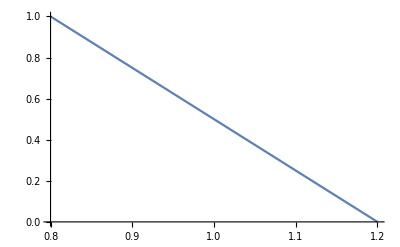

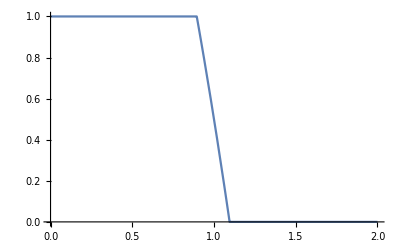

```mathematica
Series[ 1/(1 + E^("D"Δ)),{Δ,0,1}]//Normal
%/.Δ->Ee/EF-1
Solve[%==0,Ee][[1]]
Solve[%%==1,Ee][[1]]
(Ee/.%%)-(Ee/.%)//Simplify
"So in terms of momenta"
Solve[ℏ^2(ζ^2 kF^2)/(2 m)==ℏ^2 4/D kF^2/(2 m),ζ]
Plot[1/2-("D")/4(Eζ-1)/."D"->10,{Eζ,(-2+"D")/("D")/."D"->10,(2+"D")/("D")/."D"->10},PlotRange->All]
Plot[HeavisideTheta[√((-2+"D")/("D"))-ζ] +(1/2-("D")/4(ζ^2-1))HeavisideTheta[ζ-√((-2+"D")/("D"))]HeavisideTheta[√((2+"D")/("D"))-ζ]/."D"->10,(*{ζ,√((-2+"D")/("D"))/."D"->10,√((2+"D")/("D"))/."D"->10}*){ζ,0,2}]
```

```mathematica
ℏ ω<4 EF/D
```

ω ℏ<(4 EF)/D

```mathematica
Solve[4 EF/D==mχ/2(vesc^2-v^2),v]//PowerExpand
Series[v/.%[[2]],{D,∞,1}]//PowerExpand//Normal
```

{{v→-(√(-8 EF+D mχ vesc^2))/(√D √mχ)},{v→(√(-8 EF+D mχ vesc^2))/(√D √mχ)}}

-(4 EF)/(D mχ vesc)+vesc

```mathematica
"Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution."
Drescale = "D"->("D")/b/.b->1
Table[("ℏ""ωedgei"-4 ("EF")/("D"))("JpereV")^-1/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[FeTotalparams]}]//TableForm
Table[("ℏ""ωedgei"-4 ("EF")/("D"))("JpereV")^-1/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[SiO2Totalparams]}]
Table[("ℏ""ωedgei"-4 ("EF")/("D"))("JpereV")^-1/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[MgOTotalparams]}]
"So we see that expanding in energy instead of momenta made a huge difference. Now we are in line with expectation, just from the conduction band are we able to have non-zero energy transfer. And this is true independent of mass. So now we have to go back and recompute the dielectric with this correction. For the conduction band, the energy available to transfer in eV is"
(4 ("EF")/("D"))("JpereV")^-1/.Drescale/.FeTotalparams[[2]]
```

Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution.

D→D

-1.48805
-1.88182
-1.68663
-1.78616
716.214
7235.11

{-0.90446,-0.90446}

{-0.90446,-0.90446,-0.90446,-0.90446}

So we see that expanding in energy instead of momenta made a huge difference. Now we are in line with expectation, just from the conduction band are we able to have non-zero energy transfer. And this is true independent of mass. So now we have to go back and recompute the dielectric with this correction. For the conduction band, the energy available to transfer in eV is

1.88616

```mathematica
"Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution."
Drescale = "D"->("D")/b/.b->1
Table[{m,Table[-(4 "EF")/("D" mχ "vesc")+"vesc"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[-(4 "EF")/("D" mχ "vesc")+"vesc"/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[SiO2Totalparams]}]},{m,6,15}]
Table[{m,Table[-(4 "EF")/("D" mχ "vesc")+"vesc"/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[MgOTotalparams]}]},{m,6,15}]
```

Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution.

D→D

6 | -1.51454×10^7
-1.51454×10^7
-1.51454×10^7
-1.51454×10^7
-1.51454×10^7
-1.51454×10^7
7 | -1.50446×10^6
-1.50446×10^6
-1.50446×10^6
-1.50446×10^6
-1.50446×10^6
-1.50446×10^6
8 | -140366.
-140366.
-140366.
-140366.
-140366.
-140366.
9 | -3956.64
-3956.64
-3956.64
-3956.64
-3956.64
-3956.64
10 | 9684.34
9684.34
9684.34
9684.34
9684.34
9684.34
11 | 11048.4
11048.4
11048.4
11048.4
11048.4
11048.4
12 | 11184.8
11184.8
11184.8
11184.8
11184.8
11184.8
13 | 11198.5
11198.5
11198.5
11198.5
11198.5
11198.5
14 | 11199.8
11199.8
11199.8
11199.8
11199.8
11199.8
15 | 11200.
11200.
11200.
11200.
11200.
11200.

{{6,{-7.25678×10^6,-7.25678×10^6}},{7,{-715598.,-715598.}},{8,{-61479.8,-61479.8}},{9,{3932.02,3932.02}},{10,{10473.2,10473.2}},{11,{11127.3,11127.3}},{12,{11192.7,11192.7}},{13,{11199.3,11199.3}},{14,{11199.9,11199.9}},{15,{11200.,11200.}}}

{{6,{-7.25678×10^6,-7.25678×10^6,-7.25678×10^6,-7.25678×10^6}},{7,{-715598.,-715598.,-715598.,-715598.}},{8,{-61479.8,-61479.8,-61479.8,-61479.8}},{9,{3932.02,3932.02,3932.02,3932.02}},{10,{10473.2,10473.2,10473.2,10473.2}},{11,{11127.3,11127.3,11127.3,11127.3}},{12,{11192.7,11192.7,11192.7,11192.7}},{13,{11199.3,11199.3,11199.3,11199.3}},{14,{11199.9,11199.9,11199.9,11199.9}},{15,{11200.,11200.,11200.,11200.}}}

```mathematica
("βcore")^-1/.EarthRepl
("β")^-1/.FeTotalparams
("EF")/("D")/.FeTotalparams
"ℏ""ωedgei"/.FeTotalparams
```

7.55407×10^-20

{7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20}

{7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20}

{6.37768×10^-20,6.95108×10^-22,3.19641×10^-20,1.602×10^-20,1.1504×10^-16,1.15937×10^-15}

```mathematica
"D"/.FeTotalparams
"D"/.SiO2Totalparams
"D"/.MgOTotalparams
```

{17.0944,25.7168,44.3904,167.324,4306.1,90529.8}

{88.6464,257.244}

{45.6437,81.3942,92.9963,222.484}

```mathematica
("βcrust")^-1/.EarthRepl
("β")^-1/.SiO2Totalparams
("EF")/("D")/.SiO2Totalparams
("β")^-1/.MgOTotalparams
("EF")/("D")/.MgOTotalparams
```

3.62236×10^-20

{3.62236×10^-20,3.62236×10^-20}

{3.62236×10^-20,3.62236×10^-20}

{3.62236×10^-20,3.62236×10^-20,3.62236×10^-20,3.62236×10^-20}

{3.62236×10^-20,3.62236×10^-20,3.62236×10^-20,3.62236×10^-20}

### Nearly degenerate case - energy variable

#### Distribution function working with Energy instead of ζ

```mathematica
1/2-("D")/4(Eζ-1)/.Eζ->(-2+"D")/("D")//Simplify
```

1

```mathematica
Series[ 1/(1 + E^("D"Δ)),{Δ,0,1}]//Normal
%/.Δ->Ee/EF-1
Solve[%==0,Ee][[1]]
Solve[%%==1,Ee][[1]]
(Ee/.%%)-(Ee/.%)//Simplify
"So in terms of momenta"
Solve[ℏ^2(ζ^2 kF^2)/(2 m)==ℏ^2 4/D kF^2/(2 m),ζ]
Plot[1/2-("D")/4(Eζ-1)/."D"->10,{Eζ,(-2+"D")/("D")/."D"->10,(2+"D")/("D")/."D"->10},PlotRange->All]
Plot[HeavisideTheta[√((-2+"D")/("D"))-ζ] +(1/2-("D")/4(ζ^2-1))HeavisideTheta[ζ-√((-2+"D")/("D"))]HeavisideTheta[√((2+"D")/("D"))-ζ]/."D"->10,(*{ζ,√((-2+"D")/("D"))/."D"->10,√((2+"D")/("D"))/."D"->10}*){ζ,0,2}]
```

1/2-(D Δ)/4

1/2-1/4 D (-1+Ee/EF)

{Ee→((2+D) EF)/D}

{Ee→((-2+D) EF)/D}

(4 EF)/D

So in terms of momenta

{{ζ→-2/(√D)},{ζ→2/(√D)}}

-Graphics-

-Graphics-

```mathematica
ζm
```

-(ⅈ √(1/2-D))/(√D)

```mathematica
fndE=1/2-1/4 D (ζ^2-1)
Eζp = 1 + 2/D
Eζm= 1 - 2/D
ζp = 1 + 1/D
ζm = 1 -1/D
```

1/2-1/4 D (-1+ζ^2)

1+2/D

1-2/D

1+1/D

1-1/D

```mathematica
Dtemp = 300
rangerescale=8 * 2
Show[{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-rangerescale/Dtemp,1 + rangerescale/Dtemp},PlotRange->All,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{Directive[Black,Dashed],Black},{"f_FD","θ(1-ζ)"}],PlotLabel->"Occupation number - D=300",AxesLabel->Automatic],
Plot[(HeavisideTheta[1-ζ]),{ζ,1-rangerescale/Dtemp,1 + rangerescale/Dtemp},PlotStyle->Black,PlotRange->All,AxesLabel->Automatic,Exclusions->None]}]
```

300

16

-Graphics-

300

16

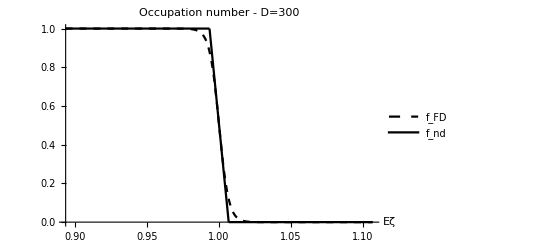

```mathematica
Dtemp = 300
rangerescale=8 * 2
Show[{Plot[(1/(1+ⅇ^(D (-1+Eζ)))/.D->Dtemp),{Eζ,1-(2 rangerescale)/Dtemp,1 + (2 rangerescale)/Dtemp},PlotRange->All,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{Directive[Black,Dashed],Black},{"f_FD","f_nd"}],PlotLabel->"Occupation number - D=300",AxesLabel->Automatic],Plot[(1/2-1/4 "D" (-1+Eζ)/."D"->Dtemp),{Eζ,1-2/Dtemp,1 + 2/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-Eζ],{Eζ,1-(2 rangerescale)/Dtemp,1-2/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-Eζ],{Eζ,1+2/Dtemp,1+(2 rangerescale)/Dtemp},PlotRange->All,PlotStyle->Black]}]
```

#### Initial and final states

```mathematica
{Eζm-(ℏ ω)/("EF"), ζ^2, Eζp}
%/.ζ->ζ+2 z//Expand
%-(4 z^2+4 z ζ)//Simplify
```

{Eζm-(ω ℏ)/EF,ζ^2,Eζp}

{Eζm-(ω ℏ)/EF,4 z^2+4 z ζ+ζ^2,Eζp}

{Eζm-4 z (z+ζ)-(ω ℏ)/EF,ζ^2,Eζp-4 z (z+ζ)}

#### Scattering Phase space

```mathematica
Solve[z == 1/2(√(1+2/D +(ℏ aω)/("EF"))- √(1 - 2/D)),aω][[1]]//Simplify
Series[aω/.%,{D,∞,1}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{aω→(4 EF (-1+D z (√((-2+D)/D)+z)))/(D ℏ)}

(4 EF z (1+z))/ℏ-(4 (EF (1+z)))/(ℏ D)+O[1/D]^2

```mathematica
Solve[z == 1/2(√(1+2/D)- √(1 - 2/D)),z][[1]]//Simplify
Series[z/.%,{D,∞,3}]
```

{z→1/2 (-√((-2+D)/D)+√((2+D)/D))}

1/D+1/(2 D^3)+O[1/D]^4

```mathematica
Series[√(1+2/D),{D,∞,1}]
Series[√(1-2/D),{D,∞,1}]
```

1+1/D+O[1/D]^2

1-1/D+O[1/D]^2

```mathematica
ℏ ω<4 EF/D
```

ω ℏ<(4 EF)/D

```mathematica
Solve[4 EF/D==mχ/2(vesc^2-v^2),v]//PowerExpand
Series[v/.%[[2]],{D,∞,1}]//PowerExpand//Normal
```

{{v→-(√(-8 EF+D mχ vesc^2))/(√D √mχ)},{v→(√(-8 EF+D mχ vesc^2))/(√D √mχ)}}

-(4 EF)/(D mχ vesc)+vesc

```mathematica
"Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution."
Drescale = "D"->("D")/b/.b->1
Table[("ℏ""ωedgei"-4 ("EF")/("D"))("JpereV")^-1/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[FeTotalparams]}]//TableForm
Table[("ℏ""ωedgei"-4 ("EF")/("D"))("JpereV")^-1/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[SiO2Totalparams]}]
Table[("ℏ""ωedgei"-4 ("EF")/("D"))("JpereV")^-1/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[MgOTotalparams]}]
"So we see that expanding in energy instead of momenta made a huge difference. Now we are in line with expectation, just from the conduction band are we able to have non-zero energy transfer. And this is true independent of mass. So now we have to go back and recompute the dielectric with this correction. For the conduction band, the energy available to transfer in eV is"
(4 ("EF")/("D"))("JpereV")^-1/.Drescale/.FeTotalparams[[2]]
```

Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution.

D→D

-1.48805
-1.88182
-1.68663
-1.78616
716.214
7235.11

{7.99554,7.99554}

{6.86554,6.86554,6.86554,6.86554}

So we see that expanding in energy instead of momenta made a huge difference. Now we are in line with expectation, just from the conduction band are we able to have non-zero energy transfer. And this is true independent of mass. So now we have to go back and recompute the dielectric with this correction. For the conduction band, the energy available to transfer in eV is

1.88616

```mathematica
"Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution."
Drescale = "D"->("D")/b/.b->1
Table[{m,Table[-(4 "EF")/("D" mχ "vesc")+"vesc"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[-(4 "EF")/("D" mχ "vesc")+"vesc"/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[SiO2Totalparams]}]},{m,6,15}]
Table[{m,Table[-(4 "EF")/("D" mχ "vesc")+"vesc"/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[MgOTotalparams]}]},{m,6,15}]
```

Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution.

D→D

6 | -1.51454×10^7
-1.51454×10^7
-1.51454×10^7
-1.51454×10^7
-1.51454×10^7
-1.51454×10^7
7 | -1.50446×10^6
-1.50446×10^6
-1.50446×10^6
-1.50446×10^6
-1.50446×10^6
-1.50446×10^6
8 | -140366.
-140366.
-140366.
-140366.
-140366.
-140366.
9 | -3956.64
-3956.64
-3956.64
-3956.64
-3956.64
-3956.64
10 | 9684.34
9684.34
9684.34
9684.34
9684.34
9684.34
11 | 11048.4
11048.4
11048.4
11048.4
11048.4
11048.4
12 | 11184.8
11184.8
11184.8
11184.8
11184.8
11184.8
13 | 11198.5
11198.5
11198.5
11198.5
11198.5
11198.5
14 | 11199.8
11199.8
11199.8
11199.8
11199.8
11199.8
15 | 11200.
11200.
11200.
11200.
11200.
11200.

{{6,{-7.25678×10^6,-7.25678×10^6}},{7,{-715598.,-715598.}},{8,{-61479.8,-61479.8}},{9,{3932.02,3932.02}},{10,{10473.2,10473.2}},{11,{11127.3,11127.3}},{12,{11192.7,11192.7}},{13,{11199.3,11199.3}},{14,{11199.9,11199.9}},{15,{11200.,11200.}}}

{{6,{-7.25678×10^6,-7.25678×10^6,-7.25678×10^6,-7.25678×10^6}},{7,{-715598.,-715598.,-715598.,-715598.}},{8,{-61479.8,-61479.8,-61479.8,-61479.8}},{9,{3932.02,3932.02,3932.02,3932.02}},{10,{10473.2,10473.2,10473.2,10473.2}},{11,{11127.3,11127.3,11127.3,11127.3}},{12,{11192.7,11192.7,11192.7,11192.7}},{13,{11199.3,11199.3,11199.3,11199.3}},{14,{11199.9,11199.9,11199.9,11199.9}},{15,{11200.,11200.,11200.,11200.}}}

```mathematica
("βcore")^-1/.EarthRepl
("β")^-1/.FeTotalparams
("EF")/("D")/.FeTotalparams
"ℏ""ωedgei"/.FeTotalparams
```

7.55407×10^-20

{7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20}

{7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20}

{6.37768×10^-20,6.95108×10^-22,3.19641×10^-20,1.602×10^-20,1.1504×10^-16,1.15937×10^-15}

```mathematica
"D"/.FeTotalparams
"D"/.SiO2Totalparams
"D"/.MgOTotalparams
```

{17.0944,25.7168,44.3904,167.324,4306.1,90529.8}

{88.6464,257.244}

{45.6437,81.3942,92.9963,222.484}

```mathematica
("βcrust")^-1/.EarthRepl
("β")^-1/.SiO2Totalparams
("EF")/("D")/.SiO2Totalparams
("β")^-1/.MgOTotalparams
("EF")/("D")/.MgOTotalparams
```

3.62236×10^-20

{3.62236×10^-20,3.62236×10^-20}

{3.62236×10^-20,3.62236×10^-20}

{3.62236×10^-20,3.62236×10^-20,3.62236×10^-20,3.62236×10^-20}

{3.62236×10^-20,3.62236×10^-20,3.62236×10^-20,3.62236×10^-20}

```mathematica
"We also have the constraint"
Solve[mχ/(2 ℏ)(vesc^2-vχ^2)==4/(β ℏ),vχ]//PowerExpand//Simplify
```

We also have the constraint

{{vχ→-(√(-8+mχ vesc^2 β))/(√mχ √β)},{vχ→(√(-8+mχ vesc^2 β))/(√mχ √β)}}

```mathematica
Re[√-2]
```

0

```mathematica
Log10@2980.110319634994
```

3.47423

```mathematica
10^3.85
```

7079.46

#### Phase space constraint from kinematics

```mathematica
ωp = q v + (ℏ q^2)/(2 mχ)
ωm = q v - (ℏ q^2)/(2 mχ)
ωm - ω > 0 
ωp + ω > 0
```

q v+(q^2 ℏ)/(2 mχ)

q v-(q^2 ℏ)/(2 mχ)

q v-ω-(q^2 ℏ)/(2 mχ)>0

q v+ω+(q^2 ℏ)/(2 mχ)>0

```mathematica
ωm + aω > 0 
ωp - aω > 0
```

aω+q v-(q^2 ℏ)/(2 mχ)>0

-aω+q v+(q^2 ℏ)/(2 mχ)>0

```mathematica
Solve[- mχ v + √(2 mχ(mχ/2 v^2+ aω ℏ))== 2 ℏ kF zndmax,aω][[1]]
ℏ aω<(ℏ aω/.%)
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{aω→(2 (kF mχ v zndmax+kF^2 zndmax^2 ℏ))/mχ}

aω ℏ<(2 ℏ (kF mχ v zndmax+kF^2 zndmax^2 ℏ))/mχ

```mathematica
Solve[mχ/(2 ℏ)(vesc^2-v^2)==2/mχ ℏ kF^2/D^2+2 v kF/D,v]
```

{{v→(-D mχ vesc-2 kF ℏ)/(D mχ)},{v→(D mχ vesc-2 kF ℏ)/(D mχ)}}

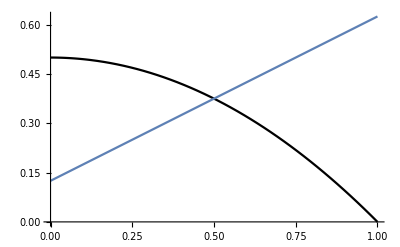

```mathematica
Show[{Plot[mχ/(2 ℏ)(vesc^2-v^2)/.{vesc->1,mχ->1,ℏ->1,D->4,kF->1},{v,0,1},PlotRange->All,PlotStyle->Black],
Plot[2/mχ ℏ kF^2/D^2+2 v kF/D/.{vesc->1,mχ->1,ℏ->1,D->4,kF->1},{v,0,1}]}]
```

#### Plot of constraints

```mathematica
"ℏ""JpereV"/.FeTotalparams[[2]]
```

1.69011×10^-53

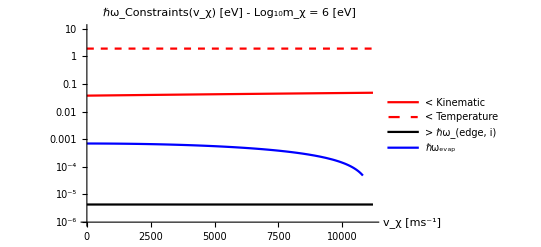

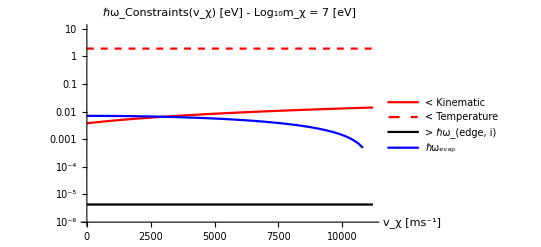

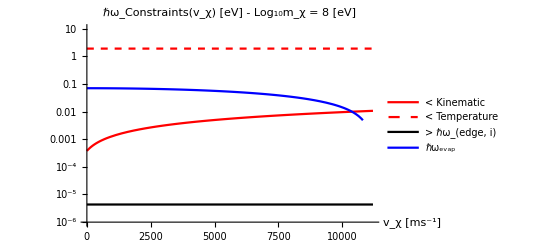

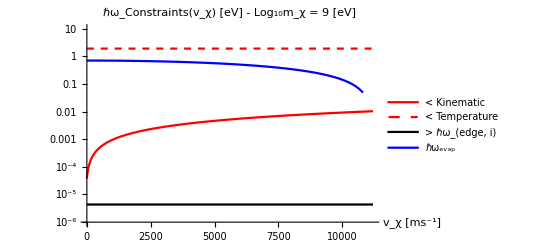

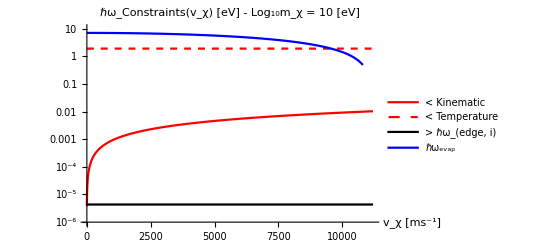

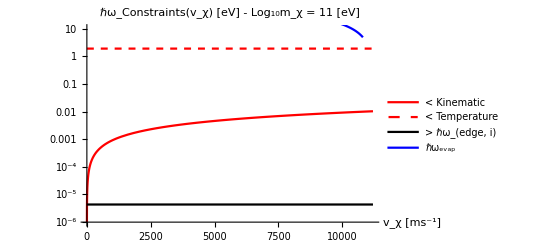

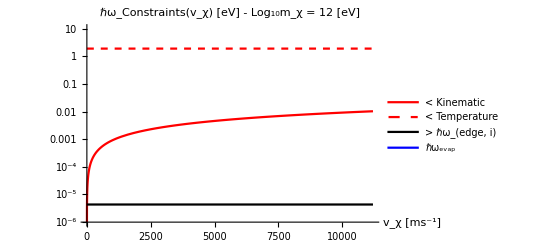

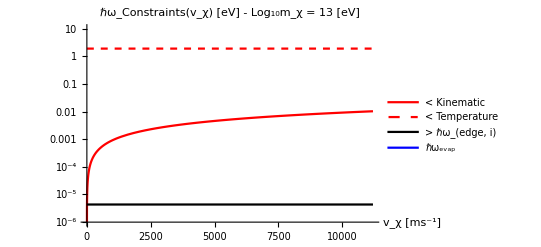

```mathematica
Do[Print@Show[{LogPlot[("ℏ")/("JpereV")(2 vχ ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ")/.RescaleParams[FeTotalparams[[2]],10^-3,"ωedgei"]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,{vχ,0,"vesc"/.EarthRepl},PlotStyle->Red,PlotRange->{10^-6,10},(*PlotRange->All,*)PlotLegends->LineLegend[{Red,Directive[Red,Dashed],Black,Blue},{"< Kinematic","< Temperature","> ℏω_(edge, i)","ℏω_evap"}],PlotLabel->StringForm["ℏω_Constraints(v_χ) [eV] - Log_10m_χ = `` [eV]",ToString[m]],AxesLabel->{"v_χ [ms^-1]"}],LogPlot[("ℏ")/("JpereV")4/("β""ℏ")/.RescaleParams[FeTotalparams[[2]],10^-3,"ωedgei"],{vχ,0,"vesc"/.EarthRepl},PlotStyle->Directive[Red,Dashed]],LogPlot[("ℏ")/("JpereV")"ωedgei"/.RescaleParams[FeTotalparams[[2]],10^-3,"ωedgei"],{vχ,0,"vesc"/.EarthRepl},PlotStyle->Black],
LogPlot[("ℏ")/("JpereV")mχ/(2 "ℏ")(("vesc"/.EarthRepl)^2-vχ^2)/.mχ->10^m("JpereV")/("c")^2/.RescaleParams[FeTotalparams[[2]],10^-3,"ωedgei"],{vχ,0,"vesc"/.EarthRepl},PlotStyle->Blue]}],{m,6,15}]
```

#### ftilde

```mathematica
1/2 (ζ^2/2+(D ζ^2)/2-(D ζ^3)/3)
```

```mathematica
ftildeE = Integrate[ζ fndE,ζ]//Simplify
```

1/16 ζ^2 (4-D (-2+ζ^2))

```mathematica
"nearly degenerate case boundary term"
"Real part"
ReBound =ftildeE  Integrate[Re[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
"Imaginary part"
ImBound =ftildeE Integrate[Im[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
```

nearly degenerate case boundary term

Real part

1/32 ζ^2 (4-D (-2+ζ^2)) Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)]

Imaginary part

1/16 ζ^2 (4-D (-2+ζ^2)) (ArcTan[(a-ζ)/uν]-ArcTan[(a+ζ)/uν])

```mathematica
"nearly Degenerate case integral bulk"
"Real part"
ReBulk=-Integrate[ftildeE Re[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify,ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(*(%/.ζ->1)-(%/.ζ->0)//FullSimplify*)
"Imaginary part"
ImBulk=-Integrate[ftildeE Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify],ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(*(%/.ζ->1)-(%/.ζ->0)//FullSimplify*)
```

nearly Degenerate case integral bulk

Real part

1/8 a ((4+D (2-a^2+3 uν^2)) ζ-(D ζ^3)/3+2 uν (2+D (1-a^2+uν^2)) ArcTan[(a-ζ)/uν]-2 uν (2+D (1-a^2+uν^2)) ArcTan[(a+ζ)/uν]-((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[a^2+uν^2-2 a ζ+ζ^2])/(4 a)+((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[a^2+uν^2+2 a ζ+ζ^2])/(4 a))

Imaginary part

-1/16 uν (-2 (4+D (2-3 a^2+uν^2)) ζ+(2 D ζ^3)/3+((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) ArcTan[(-a+ζ)/uν])/uν+((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) ArcTan[(a+ζ)/uν])/uν-2 a (2+D (1-a^2+uν^2)) Log[a^2+uν^2-2 a ζ+ζ^2]+2 a (2+D (1-a^2+uν^2)) Log[a^2+uν^2+2 a ζ+ζ^2])

```mathematica
ReTotal = ReBound+ReBulk//FullSimplify
ImTotal = ImBound+ImBulk//FullSimplify
```

1/32 (4 a (4+D (2-a^2+3 uν^2)) ζ-4/3 a D ζ^3+8 a uν (2+D (1-a^2+uν^2)) ArcTan[(a-ζ)/uν]-8 a uν (2+D (1-a^2+uν^2)) ArcTan[(a+ζ)/uν]-(a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[uν^2+(a-ζ)^2]+ζ^2 (4-D (-2+ζ^2)) Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)]+(a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[uν^2+(a+ζ)^2])

1/16 (2/3 uν ζ (12-D (-6+9 a^2-3 uν^2+ζ^2))+(a^4 D-2 a^2 (2+D+3 D uν^2)+(uν^2+ζ^2) (4+D (2+uν^2-ζ^2))) ArcTan[(a-ζ)/uν]-(a^4 D-2 a^2 (2+D+3 D uν^2)+(uν^2+ζ^2) (4+D (2+uν^2-ζ^2))) ArcTan[(a+ζ)/uν]+2 a uν (-2+D (-1+a^2-uν^2)) (-Log[uν^2+(a-ζ)^2]+Log[uν^2+(a+ζ)^2]))

```mathematica
ReTotalWbounds=(ReTotal/.ζ->1+1/D- 2 zt/D )-(ReTotal/.ζ->1-1/D )//Simplify; (*zt = D z*)
ImTotalWbounds=(ImTotal/.ζ->1+1/D- 2 zt/D )-(ImTotal/.ζ->1-1/D )//Simplify;
```

```mathematica
Limit[ReTotalWbounds ,D->∞]
Limit[ImTotalWbounds ,D->∞]
```

0

0

```mathematica
Limit[ReTotalWbounds D,D->∞]
Limit[ImTotalWbounds D,D->∞]
```

-1/2 (-1+zt^2) Log[1+(4 a)/((-1+a)^2+uν^2)]

-1/2 ⅈ (-1+zt^2) (Log[1-(ⅈ (-1+a))/uν]-Log[1+(ⅈ (-1+a))/uν]-Log[1-(ⅈ (1+a))/uν]+Log[1+(ⅈ (1+a))/uν])

See the previous approach with the momentum variable. The imaginary part is Arctan - this is h(a,u_ν)

```mathematica
(ReBound/.ζ->1+1/D- 2 zt/D)-(ReBound/.ζ->1-1/D)//Simplify
Limit[%,D->∞]
1/4 (ζ^2/2+(D ζ^2)/2-(D ζ^3)/3) Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)];
(%/.ζ->1+1/D- 2 zt/D)-(%/.ζ->1-1/D)//Simplify
Limit[%,D->∞]
```

(-(-1+D)^2 (-1+6 D+D^2) Log[1+(4 a (-1+D))/(D ((-1+a+1/D)^2+uν^2))]+(4 D+2 D^2-(1+D-2 zt)^2) (1+D-2 zt)^2 Log[1+(4 a (1+D-2 zt))/(D (uν^2+(-1+(-1+a) D+2 zt)^2/D^2))])/(32 D^3)

-(a (-1+a^2+uν^2) (-1+zt))/(4 (1-2 a+a^2+uν^2) (1+2 a+a^2+uν^2))

(-(-1+D)^2 (5+D) Log[1+(4 a (-1+D))/(D ((-1+a+1/D)^2+uν^2))]+(1+D-2 zt)^2 (1+D+4 zt) Log[1+(4 a (1+D-2 zt))/(D (uν^2+(-1+(-1+a) D+2 zt)^2/D^2))])/(24 D^2)

-(a (-1+a^2+uν^2) (-1+zt))/(3 (1-2 a+a^2+uν^2) (1+2 a+a^2+uν^2))

```mathematica
(ReBulk/.ζ->1+1/D- 2 zt/D)-(ReBulk/.ζ->1-1/D)//Simplify
Limit[%,D->∞]
```

1/8 a ((-1+D)^3/(3 D^2)+((-1+D) (-4+D (-2+a^2-3 uν^2)))/D-((-4+D (-2+a^2-3 uν^2)) (1+D-2 zt))/D-(1+D-2 zt)^3/(3 D^2)+2 uν (2+D (1-a^2+uν^2)) ArcTan[(1+a-1/D)/uν]-2 uν (2+D (1-a^2+uν^2)) ArcTan[(-1+a+1/D)/uν]-2 uν (2+D (1-a^2+uν^2)) ArcTan[(1+D+a D-2 zt)/(D uν)]+2 uν (2+D (1-a^2+uν^2)) ArcTan[(-1+(-1+a) D+2 zt)/(D uν)]+((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[1-2 a+a^2+1/D^2+(2 (-1+a))/D+uν^2])/(4 a)-((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[1+2 a+a^2+1/D^2-(2 (1+a))/D+uν^2])/(4 a)-((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[a^2+uν^2-(2 a (1+D-2 zt))/D+(1+D-2 zt)^2/D^2])/(4 a)+((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[a^2+uν^2+(2 a (1+D-2 zt))/D+(1+D-2 zt)^2/D^2])/(4 a))

(a (-1+a^2+uν^2) (-1+zt))/(4 (a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2))

### Bethe Stopping Comparison

#### Definitions

```mathematica
S0 = HoldForm[Integrate[D[f[W],W],{W,0,∞}]]
I0 = Exp[1/S0 HoldForm[Integrate[Log[W] D[f[W],W],{W,0,∞}]]]
```

∫_0^∞ ∂_W f[W]ⅆW

ⅇ^((∫_0^∞ Log[W] ∂_W f[W]ⅆW)/(∫_0^∞ ∂_W f[W]ⅆW))

```mathematica
Clear[S0,I0]
Solve[Log[(2 me c^2)/Ip0]==S0/Z Log[(2 me c^2)/I0] + D0/(2 Z),Ip0]//Simplify
```

{{Ip0→ConditionalExpression[2 c^2 ⅇ^(-(D0+2 S0 Log[(2 c^2 me)/I0])/(2 Z)) me, -2 π<Im[(D0+2 S0 Log[(2 c^2 me)/I0])/Z]≤2 π]}}

## Bethe-Bloch Analytics

#### Defn

```mathematica
dEdlBethe[vχ_,ne_,mχ_,I_:286]:=(*
vχ - [m s^-1],
ne - [m^-3], 
mχ - [Subscript[Log, 10] eV],
I - [eV] (default is for Iron)

Output: dE/dl - [eV m^-1]
*)("JpereV")^-1( (2 π ("e")^4 ("c")^2)/((4π)^2("ϵ0")^2 10^6/2"JpereV"vχ^2))nFe( Log@(1/I(2 ("m"vχ^2)/("JpereV"))) - Log[1/(1-vχ^2/("c")^2)]-vχ^2/("c")^2 - 1/2 (Log[R]+(10^(6-m)/2(γ^2-1)/γ R)^2/.R->(1+10^(2(6-m))/4+γ 10^(6-m))/.γ->1/(√(1- vχ^2/("c")^2)))(*+(("c""α")/vχ)^2Zeta[3]*))/.Constants`SIConstRepl
```

### Plot / Compare to our interpolations

#### Load e σ Dicts

```mathematica
FeσDicte=ReadIt[NotebookDirectory[]<>"../capture/FeσDicte"];
SiO2σDicte=ReadIt[NotebookDirectory[]<>"../capture/SiO2σDicte"];
MgOσDicte=ReadIt[NotebookDirectory[]<>"../capture/MgOσDicte"];
```

```mathematica
ElectronicσDicts=Gather[Flatten@Join[FeσDicte,SiO2σDicte,MgOσDicte],#1["mχ"]==#2["mχ"]&];
```

#### EL func Defn - from capture

```mathematica
Clear[GeteELFunction]
GeteELFunction[ElectronicσDicsts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[ElectronicσDicsts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;


(*Returns: ΔE[bE,vχ]*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

#### Bethe + Shell Corrections Only - Core

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
```

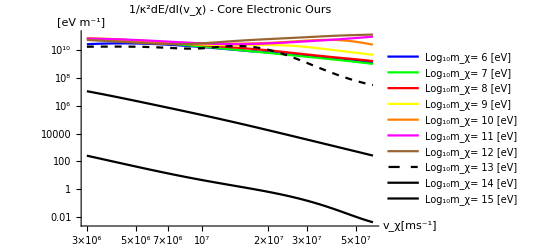

```mathematica
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ])
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic Ours",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

1.40188×10^29

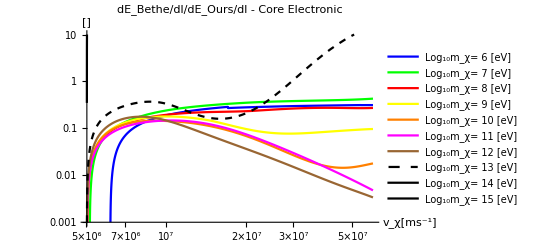

```mathematica
nFe=13000/("M")/.FeTotalparams[[1]]
(*Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1( (2 π ("e")^4 ("c")^2)/(("ϵ0")^2 10^m "JpereV"vχ^2))nFe ( Log@(1/286(2 10^m vχ^2/("c")^2)) - Log[1/(1-vχ^2/("c")^2)]-vχ^2/("c")^2)/.Constants`SIConstRepl)/((("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ]))
,{m,6,15}]],{vχ,"vesc"/.EarthRepl,10^7},AxesLabel->{"v_(χ\)[ms^-1]","[]"},PlotLabel->"dE_Bethe/dl/dE_Ours/dl - Core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]*)
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
dEdlBethe[vχ,nFe,m,286]/((("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ]))
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"dE_Bethe/dl/dE_Ours/dl - Core Electronic",PlotStyle->plotstyle,PlotRange->{0.001,10},PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

```mathematica
N@Log[26]
```

3.2581

1.40188×10^29

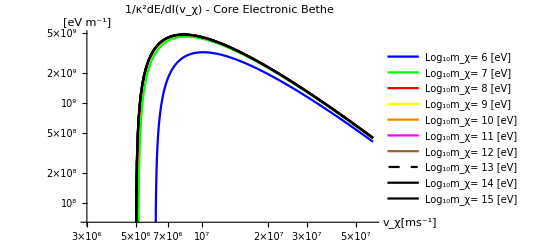

```mathematica
(*nFe=13000/("M")/.FeTotalparams[[1]]
Quiet@LogLogPlot[Evaluate[Table[
("JpereV")^-1( (2 π ("e")^4 ("c")^2)/((4π)^2("ϵ0")^2 10^6/2"JpereV"vχ^2))nFe( Log@(1/286(2 ("m"vχ^2)/("JpereV"))) - Log[1/(1-vχ^2/("c")^2)]-vχ^2/("c")^2 - 2 Log[1 +  10^(6-m)/2]+(("c""α")/vχ)^2 Zeta[3])/.Constants`SIConstRepl
,{m,6,15}]],{vχ,3 10^6,10^8},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic Bethe",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]*)
nFe=13000/("M")/.FeTotalparams[[1]]
Quiet@LogLogPlot[Evaluate[Table[
dEdlBethe[vχ,nFe,m,286]
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic Bethe",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

#### Bethe + Shell Corrections Only - Mantle

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
```

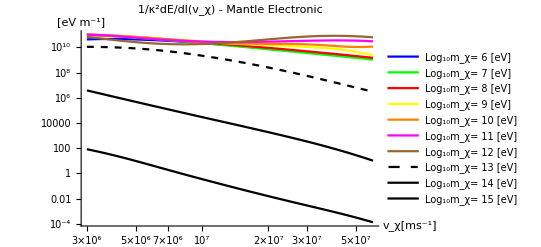

```mathematica
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[5 10^6,vχ])
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Mantle Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

```mathematica
nMgO=("MgOFrac""ρMgO")/("M"/.MgOTotalparams[[1]])/.EarthRepl/.MassDensities
nSiO2=("SiO2Frac""ρSiO2")/("M"/.SiO2Totalparams[[1]])/.EarthRepl/.MassDensities
"From Seltzer, the mean excitation energy prescription for compounds is"
```

1.49403×10^28

1.27738×10^28

From Seltzer, the mean excitation energy prescription for compounds is

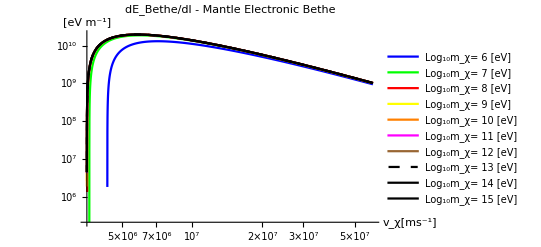

```mathematica
Quiet@LogLogPlot[Evaluate@Table[
(dEdlBethe[vχ,nMgO,m,143]+dEdlBethe[vχ,nSiO2,m,139])/.Constants`SIConstRepl
,{m,6,15}],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"dE_Bethe/dl - Mantle Electronic Bethe",PlotStyle->plotstyle,PlotRange->All(*{0.001,100}*),PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

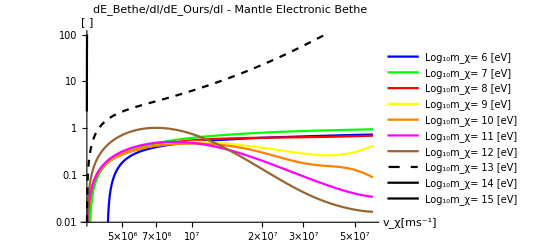

```mathematica
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(dEdlBethe[vχ,nMgO,m,143]+dEdlBethe[vχ,nSiO2,m,139])/((("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[5 10^6,vχ]))/.Constants`SIConstRepl
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[ ]"},PlotLabel->"dE_Bethe/dl/dE_Ours/dl - Mantle Electronic Bethe",PlotStyle->plotstyle,PlotRange->{0.01,100},PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

### Mean Excitation Energy

```mathematica
"The drude dielectric is the OOS used in the computation of the mean excitation energy. Drude is"
ImϵDrude = ("νi" ("ωp")^2#)/(("νi")^2#^2 + (("ωp")^2-#^2)^2)&
lnIintegrand = 2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&
ϵDrude = 1 - ("ωp")^2/(#(#+I "νi"))&
```

The drude dielectric is the OOS used in the computation of the mean excitation energy. Drude is

(νi ωp^2 #1)/(νi^2 #1^2+(ωp^2-#1^2)^2)&

(2 #1 Log[ℏ #1] ImϵDrude[#1])/(π ωp^2)&

1-ωp^2/(#1 (#1+ⅈ νi))&

#### Sum Rule - from imaginary part

```mathematica
"Numerically we see that it holds"
NIntegrate[2/(π ("ωp")^2)# ImϵDrude[#]&[ω]/.FeTotalparams,{ω,10^11,10^25},Method->"LocalAdaptive"]
```

Numerically we see that it holds

{1.,1.,1.,1.,1.,1.}

```mathematica
Table[NIntegrate["Ai"2/(π ("ωp")^2)# ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^25},Method->"LocalAdaptive"],{i,Length[FeTotalparams]}]
Total[%]
Total["Ai"/.FeTotalparams]
"Even with the truncations, to approximately the same precision as we have enforced on sum_i A_i = 1"
```

{0.209472,0.0699144,0.386622,0.234383,0.00107965,1.38466×10^-6}

0.901473

0.901844

Even with the truncations, to approximately the same precision as we have enforced on sum_i A_i = 1

```mathematica
Integrate[ω ImϵDrude[ω],ω]
Limit[%,ω->0]
Limit[%%,ω->∞]
```

(ωp^2 (-√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)) ArcTan[(√2 ω)/(√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)))]+√(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)) ArcTan[(√2 ω)/(√(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)))]))/(√2 √(νi^2-4 ωp^2))

0

(ωp^2 (-π/(2 √(1/(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2))))+π/(2 √(1/(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2))))))/(√2 √(νi^2-4 ωp^2))

```mathematica
(("ωp")^2 (-π/(2 √(1/(("νi")^2-2 ("ωp")^2-"νi" √(("νi")^2-4 ("ωp")^2))))+π/(2 √(1/(("νi")^2-2 ("ωp")^2+"νi" √(("νi")^2-4 ("ωp")^2))))))/(√2 √(("νi")^2-4 ("ωp")^2))//PowerExpand//FullSimplify
```

(ωp^2 (-√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2))+√(-2 ωp^2+νi (νi+√(νi^2-4 ωp^2)))) π)/(2 √2 √(νi^2-4 ωp^2))

```mathematica
Im[-1/(1 - ωp^2/(ω(ω+I ν)))]//ComplexExpand//Simplify
Integrate[ω %,{ω,0,∞}]
```

(ν ω ωp^2)/(ν^2 ω^2+(ω^2-ωp^2)^2)

ConditionalExpression[(ⅈ π ν ωp^2)/(√2 (√(-ν^2+2 ωp^2-√(ν^4-4 ν^2 ωp^2))+√(-ν^2+2 ωp^2+√(ν^4-4 ν^2 ωp^2)))), ]

```mathematica
Integrate[ω ImϵDrude[ω],{ω,0,∞}]
```

ConditionalExpression[(ⅈ νi ωp^2 π)/(√2 (√(-νi^2+2 ωp^2-√(νi^4-4 νi^2 ωp^2))+√(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)))), ]

#### Sum Rule - From complex drude

```mathematica
-1/ϵDrude[ω]//Simplify
```

-1/(1-ωp^2/(ω (ⅈ νi+ω)))

```mathematica
Integrate[ω-1/ϵDrude[ω],ω]
Assuming[{ω,"νi","ωp"}∈ Reals,Assuming[{ω,"νi","ωp"}∈ Reals,ComplexExpand[Im[%]]//Simplify]//Simplify]
Limit[%,ω->∞]-Limit[%,ω->0]//Simplify
(*
Limit[%,ω->0]//Simplify
Limit[%%,ω->∞]//Simplify*)
```

1/4 (-2 ω^2+(4 ⅈ νi ωp^2 ArcTan[(ⅈ νi+2 ω)/(√(νi^2-4 ωp^2))])/(√(νi^2-4 ωp^2))-2 ⅈ ωp^2 ArcTan[(νi ω)/(-ωp^2+ω^2)]-ωp^2 Log[ωp^4+νi^2 ω^2-2 ωp^2 ω^2+ω^4])

1/4 ωp^2 (-Arg[ωp^4+νi^2 ω^2-2 ωp^2 ω^2+ω^4]+Arg[1+(ⅈ νi ω)/(ωp^2-ω^2)]-Arg[1+(ⅈ νi ω)/(-ωp^2+ω^2)]-1/(√Abs[νi^2-4 ωp^2])νi (2 Arg[1+(νi-2 ⅈ ω)/(√(νi^2-4 ωp^2))] Cos[1/2 Arg[νi^2-4 ωp^2]]-2 Arg[1+(-νi+2 ⅈ ω)/(√(νi^2-4 ωp^2))] Cos[1/2 Arg[νi^2-4 ωp^2]]+(-Log[νi^2+4 ω^2+Abs[νi^2-4 ωp^2]+2 √Abs[νi^2-4 ωp^2] (νi Cos[1/2 Arg[νi^2-4 ωp^2]]-2 ω Sin[1/2 Arg[νi^2-4 ωp^2]])]+Log[νi^2+4 ω^2+Abs[νi^2-4 ωp^2]+√Abs[νi^2-4 ωp^2] (-2 νi Cos[1/2 Arg[νi^2-4 ωp^2]]+4 ω Sin[1/2 Arg[νi^2-4 ωp^2]])]) Sin[1/2 Arg[νi^2-4 ωp^2]]))

$Aborted

#### Direct integration

```mathematica
Integrate[lnIintegrand[ω],ω]//FullSimplify
```

1/(2 √2 √(νi^4-4 νi^2 ωp^2) π)νi (4 (√(-νi^2+2 ωp^2-√(νi^4-4 νi^2 ωp^2)) ArcTanh[ω/(√(-νi^2/2+ωp^2-1/2 √(νi^4-4 νi^2 ωp^2)))]-√(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)) ArcTanh[(√2 ω)/(√(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)))]) Log[ℏ ω]+√(-νi^2+2 ωp^2-√(νi^4-4 νi^2 ωp^2)) (-4 PolyLog[2,ω/(√(-νi^2/2+ωp^2-1/2 √(νi^4-4 νi^2 ωp^2)))]+PolyLog[2,-(2 ω^2)/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))])+√(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)) (4 PolyLog[2,(√2 ω)/(√(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)))]-PolyLog[2,(2 ω^2)/(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2))]))

```mathematica
Limit[1/(2 √2 √(("νi")^4-4 ("νi")^2 ("ωp")^2) π)"νi" (4 (√(-("νi")^2+2 ("ωp")^2-√(("νi")^4-4 ("νi")^2 ("ωp")^2)) ArcTanh[ω/(√(-("νi")^2/2+("ωp")^2-1/2 √(("νi")^4-4 ("νi")^2 ("ωp")^2)))]-√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)) ArcTanh[(√2 ω)/(√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)))]) Log["ℏ" ω]+√(-("νi")^2+2 ("ωp")^2-√(("νi")^4-4 ("νi")^2 ("ωp")^2)) (-4 PolyLog[2,ω/(√(-("νi")^2/2+("ωp")^2-1/2 √(("νi")^4-4 ("νi")^2 ("ωp")^2)))]+PolyLog[2,-(2 ω^2)/(("νi")^2-2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2))])+√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)) (4 PolyLog[2,(√2 ω)/(√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)))]-PolyLog[2,(2 ω^2)/(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2))])),ω->0]
```

0

```mathematica
Limit[1/(2 √2 √(("νi")^4-4 ("νi")^2 ("ωp")^2) π)"νi" (4 (√(-("νi")^2+2 ("ωp")^2-√(("νi")^4-4 ("νi")^2 ("ωp")^2)) ArcTanh[ω/(√(-("νi")^2/2+("ωp")^2-1/2 √(("νi")^4-4 ("νi")^2 ("ωp")^2)))]-√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)) ArcTanh[(√2 ω)/(√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)))]) Log["ℏ" ω]+√(-("νi")^2+2 ("ωp")^2-√(("νi")^4-4 ("νi")^2 ("ωp")^2)) (-4 PolyLog[2,ω/(√(-("νi")^2/2+("ωp")^2-1/2 √(("νi")^4-4 ("νi")^2 ("ωp")^2)))]+PolyLog[2,-(2 ω^2)/(("νi")^2-2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2))])+√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)) (4 PolyLog[2,(√2 ω)/(√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)))]-PolyLog[2,(2 ω^2)/(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2))])),ω->∞]
```

(νi DirectedInfinity[π-νi^2 √(1/(νi^2-2 ωp^2-√(νi^4-4 νi^2 ωp^2))) √(1/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))) π+2 ωp^2 √(1/(νi^2-2 ωp^2-√(νi^4-4 νi^2 ωp^2))) √(1/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))) π+√(νi^4-4 νi^2 ωp^2) √(1/(νi^2-2 ωp^2-√(νi^4-4 νi^2 ωp^2))) √(1/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))) π+2 √(-νi^2+2 ωp^2-√(νi^4-4 νi^2 ωp^2)) √(1/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))) Log[-1/(√(-νi^2/2+ωp^2-1/2 √(νi^4-4 νi^2 ωp^2)))]-√(-νi^2+2 ωp^2-√(νi^4-4 νi^2 ωp^2)) √(1/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))) Log[2/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))]+√(1/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))) √(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)) Log[-2/(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2))]-2 √(1/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))) √(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)) Log[-(√2)/(√(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)))]])/(√Sign[νi^4-4 νi^2 ωp^2] √(1/Sign[νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2)]))

```mathematica
Assuming[{"ℏ","νi","ωp"}∈ Reals&&{"ℏ","νi"}>0,Integrate[lnIintegrand[ω],{ω,0,∞}]]
```

$Aborted

#### Convergence check

```mathematica
Series[lnIintegrand[ω],{ω,∞,2}]
Series[lnIintegrand[ω],{ω,0,2}]
```

(2 νi Log[ℏ ω])/(π ω^2)+O[1/ω]^3

(2 νi Log[ℏ ω] ω^2)/(ωp^4 π)+O[ω]^3

```mathematica
Integrate[(2 "νi" Log["ℏ" ω])/(π ω^2),{ω,a,∞}]
```

ConditionalExpression[(2 νi (1+Log[ℏ a]))/(a π), Im[a]≠0||Re[a]>0]

```mathematica
Integrate[(2 "νi" Log["ℏ" ω] ω^2)/(("ωp")^4 π),{ω,0,a}]
```

(2 νi a^3 (-1+3 Log[ℏ a]))/(9 ωp^4 π)

```mathematica
"So the integral should converge"
```

#### Try integrating by parts

```mathematica
Integrate[ ImϵDrude[ω],ω]//Simplify
(2/(π ("ωp")^2)# Log["ℏ"#])&[ω]%
Limit[%,ω->0]
Limit[%%,ω->∞]
```

Try integrating by parts

(ωp^2 ArcTan[(νi^2-2 ωp^2+2 ω^2)/(νi √(-νi^2+4 ωp^2))])/(√(-νi^2+4 ωp^2))

(2 ω ArcTan[(νi^2-2 ωp^2+2 ω^2)/(νi √(-νi^2+4 ωp^2))] Log[ℏ ω])/(√(-νi^2+4 ωp^2) π)

0

νi ∞ √(-1/Sign[νi^4-4 νi^2 ωp^2])

```mathematica
Integrate[Integrate[ ImϵDrude[ω],ω]D[ω Log[ℏ ω],ω],ω]
Limit[%,ω->∞]
```

(ωp^2 (-2 √2 νi √(-(νi^2-4 ωp^2)^2) ArcTan[(√2 ω)/(√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)))] Log[ω ℏ]+2 νi^2 √(-2 νi^2+8 ωp^2) ArcTan[(√2 ω)/(√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)))] Log[ω ℏ]-4 ωp^2 √(-2 νi^2+8 ωp^2) ArcTan[(√2 ω)/(√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)))] Log[ω ℏ]-2 √(-2 νi^2+8 ωp^2) √(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)) √(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)) ArcTan[(√2 ω)/(√(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)))] Log[ω ℏ]+4 √(νi^2-4 ωp^2) √(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)) ω ArcTan[(νi^2-2 ωp^2+2 ω^2)/(νi √(-νi^2+4 ωp^2))] Log[ω ℏ]+ⅈ √2 (νi √(-(νi^2-4 ωp^2)^2)-νi^2 √(-νi^2+4 ωp^2)+2 ωp^2 √(-νi^2+4 ωp^2)) PolyLog[2,-(ⅈ √2 ω)/(√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)))]-ⅈ √2 (νi √(-(νi^2-4 ωp^2)^2)-νi^2 √(-νi^2+4 ωp^2)+2 ωp^2 √(-νi^2+4 ωp^2)) PolyLog[2,(ⅈ √2 ω)/(√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)))]+ⅈ √(-2 νi^2+8 ωp^2) √(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)) √(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)) PolyLog[2,-(ⅈ √2 ω)/(√(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)))]-ⅈ √(-2 νi^2+8 ωp^2) √(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)) √(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)) PolyLog[2,(ⅈ √2 ω)/(√(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)))]))/(4 √(νi^2-4 ωp^2) √(-νi^2+4 ωp^2) √(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)))

ComplexInfinity

#### Numerical using Salvat Prescription - w truncation

```mathematica
Table[NIntegrate["Ai"2/(π ("ωp")^2)# ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
Total[%]
Total["Ai"/.FeTotalparams]
"The Ai sum isn't quite 1, which is violating the sum rule"
```

{0.209473,0.0699144,0.386622,0.234383,0.00107965,1.38467×10^-6}

0.901473

0.901844

The Ai sum isn't quite 1, which is violating the sum rule

```mathematica
"This is all only valid for sum_i Ai = 1, and is very sensitive because of the exponential (unlike in the loss calculation where it only affected things at the 10% level) so now we divide by sun_i Ai"
-(Log["JpereV"]/.SIConstRepl)/Total["Ai"/.FeTotalparams]Table[NIntegrate["Ai"2/(π ("ωp")^2)#  ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
1/Total["Ai"/.FeTotalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
E^Total[%+%%]
```

This is all only valid for sum_i Ai = 1, and is very sensitive because of the exponential (unlike in the loss calculation where it only affected things at the 10% level) so now we divide by sun_i Ai

{10.0522,3.35507,18.5533,11.2476,0.0518105,0.0000664479}

{-9.33915,-3.1189,-17.0254,-10.0099,-0.0430661,-0.0000519001}

41.4143

```mathematica
"Same  as above, divide by sum_i A_i"
1/Total["Ai"/.FeTotalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
Total[%]
E^%/("JpereV")/.SIConstRepl
"So fixing the sum on A_i, the two ways of calculating I now agree"
```

Same  as above, divide by sum_i A_i

{-9.33915,-3.1189,-17.0254,-10.0099,-0.0430661,-0.0000519001}

-39.5365

42.1574

So fixing the sum on A_i, the two ways of calculating I now agree

```mathematica
"Now do SiO2"
1/Total["Ai"/.SiO2Totalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,"ωedgei"/.SiO2Totalparams[[i]],10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}];
E^Total[%]/("JpereV")/.SIConstRepl
"and MgO"
1/Total["Ai"/.MgOTotalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.MgOTotalparams[[i]],{ω,"ωedgei"/.MgOTotalparams[[i]],10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[MgOTotalparams]}];
E^Total[%]/("JpereV")/.SIConstRepl
```

Now do SiO2

52.2152

and MgO

62.2989

#### Numerical using Salvat Prescription - no truncation

```mathematica
Table[NIntegrate["Ai"2/(π ("ωp")^2)# ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,10^11,10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
Total[%]
Total["Ai"/.FeTotalparams]
"The Ai sum isn't quite 1, which is violating the sum rule"
```

{0.209473,0.0699144,0.386622,0.234383,0.00107965,1.38467×10^-6}

0.901473

0.901844

The Ai sum isn't quite 1, which is violating the sum rule

```mathematica
"This is all only valid for sum_i Ai = 1, and is very sensitive because of the exponential (unlike in the loss calculation where it only affected things at the 10% level) so now we divide by sun_i Ai"
-(Log["JpereV"]/.SIConstRepl)/Total["Ai"/.FeTotalparams]Table[NIntegrate["Ai"2/(π ("ωp")^2)#  ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,10^11,10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
1/Total["Ai"/.FeTotalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,10^11,10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
E^Total[%+%%]
```

This is all only valid for sum_i Ai = 1, and is very sensitive because of the exponential (unlike in the loss calculation where it only affected things at the 10% level) so now we divide by sun_i Ai

{10.0522,3.35507,18.5533,11.2476,0.0518105,0.0000664479}

{-9.33915,-3.1189,-17.0254,-10.0099,-0.0430661,-0.0000519001}

41.4143

```mathematica
"Same  as above, divide by sum_i A_i"
1/Total["Ai"/.FeTotalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,10^11,10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
Total[%]
E^%/("JpereV")/.SIConstRepl
"So fixing the sum on A_i, the two ways of calculating I now agree"
```

Same  as above, divide by sum_i A_i

{-9.33915,-3.1189,-17.0254,-10.0099,-0.0430661,-0.0000519001}

-39.5365

42.1574

So fixing the sum on A_i, the two ways of calculating I now agree

```mathematica
"Now do SiO2"
1/Total["Ai"/.SiO2Totalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,10^9,10^26},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}];
E^Total[%]/("JpereV")/.SIConstRepl
"and MgO"
1/Total["Ai"/.MgOTotalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.MgOTotalparams[[i]],{ω,10^11,10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[MgOTotalparams]}];
E^Total[%]/("JpereV")/.SIConstRepl
```

Now do SiO2

39.5939

and MgO

57.6243

#### Numerical using Seltzer Prescription

```mathematica
1/Total["Ai"/.FeTotalparams] Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
Total[%]
1/Total["Ai"/.FeTotalparams] Total["Ai"π/2("ωp")^2/.FeTotalparams]
```

{1.20686×10^32,7.43262×10^31,9.32115×10^32,4.13535×10^33,2.48685×10^33,3.07458×10^32}

8.05679×10^33

9.03806×10^33

```mathematica
Total@Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
1/%Table[NIntegrate["Ai"# Log["ℏ"#]ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
(E^Total@%)/("JpereV")/.SIConstRepl
```

7.26597×10^33

{-0.602292,-0.371147,-4.59461,-19.769,-11.104,-1.28995}

256.42

```mathematica
Total@Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,10^11,10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
1/%Table[NIntegrate["Ai"# Log["ℏ"#]ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,10^11,10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
(E^Total@%)/("JpereV")/.SIConstRepl
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {2.20581×10^14}. NIntegrate obtained 3.96806×10^32 and 3.60288×10^17 for the integral and error estimates.

8.15092×10^33

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {1.72737×10^13}. NIntegrate obtained -1.08972×10^35 and 7.3787×10^19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {1.95086×10^14}. NIntegrate obtained -1.35097×10^34 and 9.22337×10^18 for the integral and error estimates.

{-0.536905,-0.330851,-4.09577,-17.6227,-13.3693,-1.65747}

288.567

```mathematica
Total@Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,"ωedgei"/.SiO2Totalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}]
1/%Table[NIntegrate["Ai"# Log["ℏ"#]ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,"ωedgei"/.SiO2Totalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}]
(E^Total@%)/("JpereV")/.SIConstRepl
```

1.56724×10^33

{-28.138,-21.7308}

0.00137264

```mathematica
Total@Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,10^10,10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}]
1/%Table[NIntegrate["Ai"# Log["ℏ"#]ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,10^10,10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}]
(E^Total@%)/("JpereV")/.SIConstRepl
```

2.00395×10^33

{-22.3205,-17.0096}

51.8202

```mathematica
Total@Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,"ωedgei"/.SiO2Totalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}]
1/%Table[NIntegrate["Ai"# Log["ℏ"#]ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,"ωedgei"/.SiO2Totalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}]
(E^Total@%)/("JpereV")/.SIConstRepl
```

1.56724×10^33

{-28.138,-21.7308}

0.00137264

```mathematica
Total@Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.MgOTotalparams[[i]],{ω,"ωedgei"/.MgOTotalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[MgOTotalparams]}]
1/%Table[NIntegrate["Ai"# Log["ℏ"#]ImϵDrude[#]&[ω]/.MgOTotalparams[[i]],{ω,"ωedgei"/.MgOTotalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[MgOTotalparams]}]
(E^Total@%)/("JpereV")/.SIConstRepl
```

3.94397×10^33

{-0.304631,-3.27401,-2.13617,-33.3193}

69.6657

```mathematica
Total@Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.MgOTotalparams[[i]],{ω,10^11,10^28},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[MgOTotalparams]}]
1/%Table[NIntegrate["Ai"# Log["ℏ"#]ImϵDrude[#]&[ω]/.MgOTotalparams[[i]],{ω,10^11,10^28},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[MgOTotalparams]}]
(E^Total@%)/("JpereV")/.SIConstRepl
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {5.38362×10^11}. NIntegrate obtained 2.99862×10^31 and 8.34588×10^21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {8.08107×10^11}. NIntegrate obtained 3.22835×10^32 and 5.36793×10^24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {1.04002×10^12}. NIntegrate obtained 2.11014×10^32 and 2.50434×10^25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

3.97569×10^33

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {4.60903×10^11}. NIntegrate obtained -1.21341×10^33 and 3.37756×10^23 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {8.42514×10^11}. NIntegrate obtained -1.29338×10^34 and 2.14659×10^26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {8.78521×10^11}. NIntegrate obtained -8.43431×10^33 and 1.00431×10^27 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{-0.305209,-3.25322,-2.12147,-33.1058}

89.3161

#### Plasma energy comparison to Seltzer

```mathematica
1/Total["Ai"/.FeTotalparams] Table[√NIntegrate["Ai"2/π#  ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^26},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}];
("ℏ")/("JpereV")Total[%]/.SIConstRepl
1/Total["Ai"/.FeTotalparams] Table[NIntegrate["Ai"2/π#  ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^26},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}];
("ℏ")/("JpereV")√Total[%]/.SIConstRepl
"so factor of 2 difference between averaging and adding in quadrature for the plasma freuqncy"
```

100.617

47.1642

so factor of 2 difference between averaging and adding in quadrature for the plasma freuqncy

```mathematica
"Ai"("M")/1000"nI"/.FeTotalparams
28.816 √(Total[%] 26/56)(*seltzer parametrization*)
```

{0.252041,0.155222,1.94661,8.6362,6.96598,0.918891}

85.304

#### Density effect

### Stopping number

#### Matching on to dEdr

```mathematica
Series[(mχ  v - √(mχ^2 v^2 - 2 mχ ℏ ω))/ℏ,{mχ,∞,1}]//PowerExpand
Series[(mχ  v + √(mχ^2 v^2 - 2 mχ ℏ ω))/ℏ,{mχ,∞,1}]//PowerExpand
```

ω/v+(ω^2 ℏ)/(2 v^3 mχ)+O[1/mχ]^2

(2 v mχ)/ℏ-ω/v-(ω^2 ℏ)/(2 v^3 mχ)+O[1/mχ]^2

```mathematica
"Stopping coefficient from stopping number"
(2 π z^2 e^4)/(m v^2)n(4 Z)/(π ωp^2)/.ωp -> √((4 π e^2 n)/m)
```

Stopping coefficient from stopping number

(2 e^2 z^2 Z)/(π v^2)

### Bloch / Lindhard Sorensen Correction

```mathematica
"From Bischell, this is the Lindhard Sorensen / Bloch correction"
```

```mathematica
LBloch = - y^2 Sum[1/l^3,{l,1,∞}] (*Summand is 1/(l (l^2+y^2))since y^2 ∝ κ^2 << 1*)
```

-y^2 Zeta[3]

```mathematica
N[Zeta[3]]
```

1.20206

```mathematica
Integrate
```

### Validity of our appraoch and bethe approaches

#### χ and v_F values in the Earth

```mathematica
"χ"/.FeTotalparams
"vF"/.FeTotalparams
```

{0.643411,0.580962,0.506851,0.363758,0.161503,0.0754231}

{1.68373×10^6,2.06517×10^6,2.71326×10^6,5.26776×10^6,2.67232×10^7,1.2253×10^8}

```mathematica
"χ"/.SiO2Totalparams
"vF"/.SiO2Totalparams
```

{0.512371,0.392567}

{2.65511×10^6,4.52297×10^6}

```mathematica
"χ"/.MgOTotalparams
"vF"/.MgOTotalparams
```

{0.604859,0.523421,0.506271,0.407075}

{1.90521×10^6,2.54418×10^6,2.71947×10^6,4.20631×10^6}

#### The Born approximation - screening length

From our notes, the characteristic screening length is k_TF^-1 where

```mathematica
kTF = √(("e")^2/("ϵ0")(3 "ne")/(2"EF"))/."EF" -> ("ℏ")^2/(2 "m")(3 π^2"ne")^(2/3)/."e"->√("α" 4 π "ϵ0" "ℏ" "c")//Simplify
```

2 √((c m ne^(1/3) α)/ℏ) (3/π)^(1/6)

```mathematica
√((kg s^-1 m^-1)/(J s))/.J->kg m s^-2
```

√(1/m^2)

This implies the characteristic range of the interaction (following Merzbacher) is

```mathematica
scatrad =kTF^-1
```

(π/3)^(1/6)/(2 √((c m ne^(1/3) α)/ℏ))

The spacing between electrons in the gas is roughly n_e^(-1/3).

So that the condition on pg293 of Merzbacher for the validity of the scattering formula used in the born approximation is

```mathematica
(scatrad^2 k)/r/.r->("ne")^(-1/3)/.k->mχ v
```

(ℏ mχ (π/3)^(1/3) v)/(4 c m α)

Does what we are doing here really rely on the Born approximation? 

Merzbacher lays out the Born approximation and the roughly the assumptions involved (that the above is small) - explain physically

Pines lays out the condition v>>v_F (I think, I couldn’t find a definition of v_0) for the born approximation as well. 

Merzbacher also lays out TDPT, and I don’t really understand the difference, it seems FGR is the correct thing. 

The physics argument from pines is that we just need to be able to treat the field of the probe as a time varying external test charge. - I can see this being related to a fast probe, since if it is moving too slowly then it can’t be treated as a plane wave, since it will be a superposition of states with widely varying momenta (does that invalidate our derivation?)

But I think all of this is helped by the fact that the amplitude for a scatter is very small, so that subsequent scatters will be very widely separated and we can treat the probe as an asymptotic plane wave. 
- but I need to understand this weakness condition. 
- soft scatters won’t affect this story, since one they would be small so won’t violate the born approximation (small loss so approximately same state) and also screening suppresses these so no enhancement.

I don' t think this is necessary for the born approximation.

#### Assumptions / physics story

Fermi's golden rule - so just TDPT
Integrating over transition rate for average energy transfered to system

Charges in the system respond to the constant electric oscillating / harmonic electric field of the probe - ie. no magnetic (and in an energy eigenstate) 
In response to the electric field the system polarizes, according to the screened / total electric field (response is then solved for self consistently)
Also assuming spin independence

Also worth noting that we share assumptions with the Bethe formula 
	- valid since they reduce to eachother
	- can support this by showing the lindhard result for large v/vF
	
For illustration can also show the wakes paper results

1409.8079_mermin_finit_temp...

A CHECK WE CAN DO IS LOOK AT ASSUMPTIONS OF RANDOM TIME APPROXIMATION IN (BONITZ?) they time scales over which we can make these assumption that the interaction behaves as a decay.

## Scrap

#### more scrap

```mathematica
Integrate
```

Here are some things that would be nice if they work, but currently don’t

```mathematica
"Degenerate case integral proper"
Integrate[Integrate[ζ ,ζ](1/(a -ζ + I uν)1/(a -ζ + I uν)),ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal
Assuming[{{a,uν,ζ}∈Reals,uν>0},Re[%]//ComplexExpand//Simplify]
Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[%%]//ComplexExpand//Simplify]
```

Degenerate case integral proper

1/2 ((a+ⅈ uν)^2/(a+ⅈ uν-ζ)+ζ+2 (-ⅈ a+uν) ArcTan[uν/(-a+ζ)]+(a+ⅈ uν) Log[a^2+uν^2-2 a ζ+ζ^2])

1/4 (-2 uν Arg[1+(ⅈ uν)/(a-ζ)]+(2 (a^3+a uν^2+2 uν^2 ζ-2 a ζ^2+ζ^3+uν (a^2+uν^2-2 a ζ+ζ^2) Arg[1+(ⅈ uν)/(-a+ζ)]+a (a^2+uν^2-2 a ζ+ζ^2) Log[a^2+uν^2-2 a ζ+ζ^2]))/(a^2+uν^2-2 a ζ+ζ^2))

1/2 (a Arg[1+(ⅈ uν)/(a-ζ)]+(a^2 uν+uν^3-2 a uν ζ-a (uν^2+(a-ζ)^2) Arg[1+(ⅈ uν)/(-a+ζ)]+uν (uν^2+(a-ζ)^2) Log[a^2+uν^2-2 a ζ+ζ^2])/(uν^2+(a-ζ)^2))

```mathematica
"degenerate case boundary term"
Integrate[ζ ,ζ]Integrate[1/(a -w + I uν),{w,-ζ,ζ},Assumptions->{{a,uν}∈Reals,uν>0}]//Normal
Limit[%,ζ->0]
Limit[%,ζ->1]
```

degenerate case boundary term

ζ^2 ArcTanh[ζ/(a+ⅈ uν)]

0

0

```mathematica
Degenint=ζ^2/2 Integrate[1/(a -w + I uν),{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
"Real part"
Assuming[{{a,uν,ζ}∈Reals,uν>0},Re[Degenint]//ComplexExpand//Simplify]
(%/.ζ->1)-(%/.ζ->0)
"Imaginary part"
Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[Degenint]//ComplexExpand]
Assuming[uν>0,(%/.ζ->1)-(%/.ζ->0)//ComplexExpand//FullSimplify]
```

ζ^2 ArcTanh[ζ/(a+ⅈ uν)]

Real part

1/4 ζ^2 Log[(a^2+uν^2+2 a ζ+ζ^2)/(a^2+uν^2-2 a ζ+ζ^2)]

1/4 Log[(1+2 a+a^2+uν^2)/(1-2 a+a^2+uν^2)]

Imaginary part

-1/2 ζ^2 Arg[1-ζ/(a+ⅈ uν)]+1/2 ζ^2 Arg[1+ζ/(a+ⅈ uν)]

1/2 (-Arg[1-1/(a+ⅈ uν)]+Arg[1+1/(a+ⅈ uν)])

Arg is related to Arctan by https://math.stackexchange.com/questions/4293260/argument-of-a-complex-number-as-arctan

#### Scrap

```mathematica
Assuming[{a,uν,ζ}∈Reals,{Re[1/(a + I uν - ζ)-1/(a + I uν + ζ)],Im[1/(a + I uν - ζ)-1/(a + I uν + ζ)]}//ComplexExpand]
Integrate[%[[1]],{ζ,0,1},Assumptions->{{a,uν}∈Reals,uν>0}]
```

{a/(uν^2+(a-ζ)^2)-ζ/(uν^2+(a-ζ)^2)-a/(uν^2+(a+ζ)^2)-ζ/(uν^2+(a+ζ)^2),-uν/(uν^2+(a-ζ)^2)+uν/(uν^2+(a+ζ)^2)}

-1/2 Log[(-1+a)^2+uν^2]+Log[a^2+uν^2]-1/2 Log[(1+a)^2+uν^2]

```mathematica
Assuming[{a,uν,ζ}∈Reals,{Re[1/(a + I uν - ζ)-1/(a + I uν + ζ)],Im[1/(a + I uν - ζ)-1/(a + I uν + ζ)]}//ComplexExpand];
(*Integrate[ζ^2%[[1]],{ζ,0,1},Assumptions->{{a,uν}∈Reals,uν>0}]//Simplify//PowerExpand//FullSimplify*)
Integrate[ζ^2/2%[[1]],ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Simplify//PowerExpand//FullSimplify
```

1/4 (-2 ζ^2-4 a uν ArcTan[(a-ζ)/uν]-4 a uν ArcTan[(a+ζ)/uν]-(a-uν) (a+uν) (Log[uν^2+(a-ζ)^2]+Log[uν^2+(a+ζ)^2]))

```mathematica
Assuming[{a,uν,ζ}∈Reals,{Re[1/(a + I uν - ζ)-1/(a + I uν + ζ)],Im[1/(a + I uν - ζ)-1/(a + I uν + ζ)]}//ComplexExpand]
(*Integrate[ζ^2%[[1]],{ζ,0,1},Assumptions->{{a,uν}∈Reals,uν>0}]//Simplify//PowerExpand//FullSimplify*)
Integrate[E^(-D ζ^2)%[[2]],{ζ,0,∞},Assumptions->{{a,uν,D}∈Reals,{D,uν}>0}]//Simplify//PowerExpand//FullSimplify
```

{a/(uν^2+(a-ζ)^2)-ζ/(uν^2+(a-ζ)^2)-a/(uν^2+(a+ζ)^2)-ζ/(uν^2+(a+ζ)^2),-uν/(uν^2+(a-ζ)^2)+uν/(uν^2+(a+ζ)^2)}

1/2 ⅈ ⅇ^(-D (a+ⅈ uν)^2) (-ExpIntegralEi[D (a+ⅈ uν)^2]-Log[-a-ⅈ uν]+ⅇ^(4 ⅈ a D uν) (ExpIntegralEi[D (a-ⅈ uν)^2]-Log[a-ⅈ uν]+Log[-a+ⅈ uν])+Log[a+ⅈ uν])

```mathematica
Assuming[{a,uν,ζ}∈Reals,{Re[ⅇ^(-D (a+ⅈ uν)^2) (-ⅈ π+ExpIntegralEi[D (a+ⅈ uν)^2])],Im[ⅇ^(-D (a+ⅈ uν)^2) (-ⅈ π+ExpIntegralEi[D (a+ⅈ uν)^2])]}//ComplexExpand]//Simplify
```

{ⅇ^(D (-a^2+uν^2)) (Cos[2 a D uν] Re[ExpIntegralEi[D (a+ⅈ uν)^2]]+(-π+Im[ExpIntegralEi[D (a+ⅈ uν)^2]]) Sin[2 a D uν]),-ⅇ^(D (-a^2+uν^2)) (π Cos[2 a D uν]-Cos[2 a D uν] Im[ExpIntegralEi[D (a+ⅈ uν)^2]]+Re[ExpIntegralEi[D (a+ⅈ uν)^2]] Sin[2 a D uν])}

```mathematica
Series[(Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)]-Log[((ap+ζ)^2+uν^2)/((ap-ζ)^2+uν^2)]),ζ ->∞]
```

(4 a-4 ap)/ζ+O[1/ζ]^3

```mathematica
Solve[mχ/(2 ℏ)(vesc^2-v^2)==ωmax,v]
```

{{v→-(√(mχ vesc^2-2 ωmax ℏ))/(√mχ)},{v→(√(mχ vesc^2-2 ωmax ℏ))/(√mχ)}}

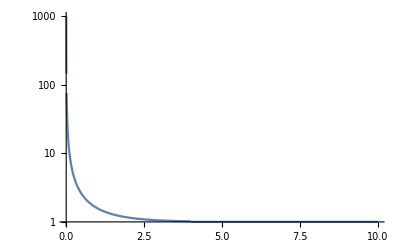

```mathematica
LogPlot[If[4 >#,If[#>0.01,1/(1-E^(- #)),1/#-1/2],1]&[ x],{x,0.001,10},PlotRange->All]
```

#### Check cross-section units

```mathematica
"The dimensionfull quantities in our dσ cross-section are"
("e")^2/(vχ^2 ("ℏ")^2 "ne" "ϵ0")/."e"->√("α" 4 π "ϵ0" "ℏ" "c")
%/."ne"->L^-3 /.vχ->L T^-1 /."ℏ"-> M L T^-1 /."c"->L T^-1
%/.M -> J L^-1 T^2
```

The dimensionfull quantities in our dσ cross-section are

(4 c α π)/(ne ℏ vχ^2)

(4 α L π T^2)/M

(4 α L^2 π)/J

```mathematica
"in the EL function they are"
"ne" ("ℏ")^2 ω^2("e")^2/(vχ^2 ("ℏ")^2 "ne" "ϵ0")/."e"->√("α" 4 π "ϵ0" "ℏ" "c")
%/."ne"->L^-3 /.vχ->L T^-1 /."ℏ"-> M L T^-1 /."c"->L T^-1/.ω->T^-1
%/.M -> J L^-1 T^2
```

in the EL function they are

(4 c α ℏ π ω^2)/vχ^2

(4 α M π)/T^2

(4 α J π)/L